```mathematica
SetDirectory["/Users/marco/marco.live/PROGRAMS/ALL-PELCR/GITHUB-current"]
```

/Users/marco/marco.live/PROGRAMS/ALL-PELCR/GITHUB-current

```mathematica
FinalNodes[k_]:=TakeValues["final nodes         :",k]
FamilyReductions[k_]:=TakeValues["family reductions   :",k]
CombustedNodes[k_]:=TakeValues["combusted nodes     :",k]
Fires[k_]:=TakeValues["fires               :",k]
ETA[k_]:=TakeValues["elapsed time        :",k]

TakeValues[text_,k_]:=(
X=ReadString["out-dd5-"<>ToString[k]<>".log"];
(*Print@StringPosition[X,"final nodes"];*)
part=Partition[Flatten[StringPosition[X,text]],2];
numparts=Map[StringTake[X,{#[[2]]+1,#[[2]]+15}]&,part];
(*Print[numparts];*)
nodes=Map[GetNumber,numparts];
(*Print["allnum = ",allnum];*)

Print[nodes];
Plus@@nodes)

GetNumber[string_]:=(
(*Print["--->",string,Select[Characters[string],DigitQ]];*)
chars=Select[Characters[string],#=!=" "&];
i=1;While[DigitQ[chars[[i]]],i++];Print[chars," ",i];
FromDigits[Map[ToExpression,Take[chars,i-1]]]
)
```

```mathematica
TakeValues["fires               :",5]
```

{1,6,2,8,1,4,8,5,
,(,9,)} 9

{1,6,1,8,9,3,4,7,
,(,3,9,)} 9

{1,6,3,1,3,7,2,6,
,(,3,1,)} 9

{1,5,5,1,5,8,9,5,
,(,2,9,)} 9

{1,6,3,2,3,5,4,7,
,(,3,7,)} 9

{1,6,2,0,7,5,8,9,
,(,3,3,)} 9

{1,5,5,7,4,6,0,8,
,(,2,8,)} 9

{1,5,8,5,5,7,2,3,
,(,3,4,)} 9

{1,6,0,0,8,3,9,0,
,(,7,)} 9

{1,5,9,0,8,3,8,5,
,(,2,1,)} 9

{1,5,9,0,2,7,3,0,
,(,1,6,)} 9

{1,5,7,1,2,5,0,2,
,(,3,0,)} 9

{1,5,2,8,4,9,1,0,
,(,1,9,)} 9

{1,6,2,2,3,8,6,3,
,(,1,8,)} 9

{1,5,9,0,2,5,2,3,
,(,2,3,)} 9

{1,5,6,2,6,9,3,2,
,(,2,0,)} 9

{1,6,4,0,6,9,1,6,
,(,5,)} 9

{1,5,3,1,0,2,1,7,
,(,2,)} 9

{1,5,5,4,6,9,6,1,
,(,3,5,)} 9

{1,6,0,3,4,3,1,3,
,(,2,5,)} 9

{1,6,5,2,7,3,3,8,
,(,1,2,)} 9

{1,6,3,3,0,8,8,3,
,(,6,)} 9

{1,5,5,0,7,2,3,5,
,(,1,4,)} 9

{1,5,4,2,1,3,2,1,
,(,3,)} 9

{1,5,6,7,1,7,9,0,
,(,3,2,)} 9

{1,6,2,7,4,7,0,7,
,(,1,5,)} 9

{1,5,8,5,4,6,0,9,
,(,1,1,)} 9

{1,5,9,7,5,5,7,8,
,(,1,7,)} 9

{1,6,2,4,8,6,2,9,
,(,2,7,)} 9

{1,5,5,2,1,9,9,0,
,(,2,6,)} 9

{1,5,5,4,0,9,6,9,
,(,4,)} 9

{1,5,5,5,2,9,0,9,
,(,3,8,)} 9

{1,6,0,8,5,2,8,3,
,(,1,0,)} 9

{1,6,1,8,4,2,4,5,
,(,0,)} 9

{1,5,5,6,4,3,7,9,
,(,3,6,)} 9

{1,5,5,8,2,2,6,8,
,(,1,)} 9

{1,6,2,4,3,3,3,7,
,(,2,4,)} 9

{1,6,4,1,5,8,3,2,
,(,1,3,)} 9

{1,5,4,4,0,5,3,3,
,(,2,2,)} 9

{1,5,8,8,4,8,1,6,
,(,8,)} 9

{16281485,16189347,16313726,15515895,16323547,16207589,15574608,15855723,16008390,15908385,15902730,15712502,15284910,16223863,15902523,15626932,16406916,15310217,15546961,16034313,16527338,16330883,15507235,15421321,15671790,16274707,15854609,15975578,16248629,15521990,15540969,15552909,16085283,16184245,15564379,15582268,16243337,16415832,15440533,15884816}

635959213

```mathematica
X
```

pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(11) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(14) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(19) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(7) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(8) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(10) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(12) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(15) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(17) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(22) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
PELCR (Parallel Environment for Lambda Calculus Optimal Reduction)
             C. Giuffrida, M. Pedicini, F. Quaglia 
                  IAC - CNR (Rome, 1996 - 2002)
(0) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(4) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(5) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(23) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(24) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(26) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(30) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(31) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(2) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(20) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(9) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(13) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(18) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(21) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(28) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(16) EVAL
(25) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(1) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(6) EVAL
(3) EVAL
pelcrexamples
pelcrexamples -> pelcrexamples -> pelcrexamples
USER TYPE Size: 64 bit
(27) EVAL
(29) EVAL
(0) PELCR 10.0>  
(0) reading from file dd5.plcr
(0) filepointer [0x56035590fa90] to pelcrexamples/dd5.plcr
 PELCR 10.0> 
 PELCR 10.0> (0) number of cut-nodes:   1(0) number of cut-nodes:   2(0) number of cut-nodes:   3(0) number of cut-nodes:   4(0) number of cut-nodes:   5(0) number of cut-nodes:   6(0) number of cut-nodes:   7(0) number of cut-nodes:   8(0) number of cut-nodes:   9(0) sending initial graph termination signals (eot)
(0) initial network created
(0) n. of activated processes 32
(22) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(27) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(31) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(28) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(29) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(4) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(4) idle loops set to 1000000000
(1) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(1) idle loops set to 1000000000
(19) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(7) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(7) idle loops set to 1000000000
(20) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(8) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(8) idle loops set to 1000000000
(10) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(9) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(11) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(12) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(21) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(15) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(13) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(14) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(2) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(2) idle loops set to 1000000000
(18) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(17) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(5) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(5) idle loops set to 1000000000
(23) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(6) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(6) idle loops set to 1000000000
(24) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(3) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(3) idle loops set to 1000000000
(16) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(16) idle loops set to 1000000000
(25) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(26) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(30) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(0) 2nd barrier - injecting the stream of actions corresponding to the parsed term
(19) idle loops set to 1000000000
(20) idle loops set to 1000000000
(10) idle loops set to 1000000000
(9) idle loops set to 1000000000
(11) idle loops set to 1000000000
(12) idle loops set to 1000000000
(15) idle loops set to 1000000000
(13) idle loops set to 1000000000
(14) idle loops set to 1000000000
(18) idle loops set to 1000000000
(17) idle loops set to 1000000000
(30) idle loops set to 1000000000
(22) idle loops set to 1000000000
(27) idle loops set to 1000000000
(28) idle loops set to 1000000000
(29) idle loops set to 1000000000
(0) idle loops set to 1000000000
(21) idle loops set to 1000000000
(23) idle loops set to 1000000000
(24) idle loops set to 1000000000
(25) idle loops set to 1000000000
(26) idle loops set to 1000000000
(17) 3rd barrier - starting the distributed computing engine
(17) running...
(30) 3rd barrier - starting the distributed computing engine
(30) running...
(22) 3rd barrier - starting the distributed computing engine
(22) running...
(31) idle loops set to 1000000000
(31) 3rd barrier - starting the distributed computing engine
(31) running...
(27) 3rd barrier - starting the distributed computing engine
(27) running...
(28) 3rd barrier - starting the distributed computing engine
(28) running...
(4) 3rd barrier - starting the distributed computing engine
(4) running...
(1) 3rd barrier - starting the distributed computing engine
(1) running...
(29) 3rd barrier - starting the distributed computing engine
(29) running...
(7) 3rd barrier - starting the distributed computing engine
(7) running...
(19) 3rd barrier - starting the distributed computing engine
(19) running...
(8) 3rd barrier - starting the distributed computing engine
(8) running...
(20) 3rd barrier - starting the distributed computing engine
(20) running...
(10) 3rd barrier - starting the distributed computing engine
(10) running...
(9) 3rd barrier - starting the distributed computing engine
(9) running...
(11) 3rd barrier - starting the distributed computing engine
(11) running...
(0) 3rd barrier - starting the distributed computing engine
(0) running...
(12) 3rd barrier - starting the distributed computing engine
(12) running...
(15) 3rd barrier - starting the distributed computing engine
(15) running...
(13) 3rd barrier - starting the distributed computing engine
(13) running...
(2) 3rd barrier - starting the distributed computing engine
(2) running...
(14) 3rd barrier - starting the distributed computing engine
(14) running...
(18) 3rd barrier - starting the distributed computing engine
(18) running...
(5) 3rd barrier - starting the distributed computing engine
(5) running...
(21) 3rd barrier - starting the distributed computing engine
(21) running...
(6) 3rd barrier - starting the distributed computing engine
(6) running...
(23) 3rd barrier - starting the distributed computing engine
(23) running...
(3) 3rd barrier - starting the distributed computing engine
(3) running...
(16) 3rd barrier - starting the distributed computing engine
(16) running...
(24) 3rd barrier - starting the distributed computing engine
(24) running...
(25) 3rd barrier - starting the distributed computing engine
(25) running...
(26) 3rd barrier - starting the distributed computing engine
(26) running...

```mathematica
ETA[5]
```

{3,
,(,2,),f} 2

{3,
,(,1,9,)} 2

{3,
,(,1,0,)} 2

{3,
,(,5,),f} 2

{3,
,(,4,),f} 2

{3,
,(,2,6,)} 2

{3,
,(,3,1,)} 2

{3,
,(,2,8,)} 2

{3,
,(,1,2,)} 2

{3,
,(,9,),f} 2

{3,
,(,3,0,)} 2

{3,
,(,7,),f} 2

{3,
,(,1,1,)} 2

{3,
,(,1,),f} 2

{3,
,(,2,5,)} 2

{3,
,(,2,7,)} 2

{3,
,(,2,1,)} 2

{3,
,(,1,7,)} 2

{3,
,(,2,0,)} 2

{3,
,(,2,9,)} 2

{3,
,(,3,),f} 2

{3,
,(,2,4,)} 2

{3,
,(,2,3,)} 2

{3,
,(,1,4,)} 2

{3,
,(,8,),f} 2

{3,
,(,1,8,)} 2

{3,
,(,6,),f} 2

{3,
,(,1,5,)} 2

{3,
,(,1,3,)} 2

{3,
,(,1,6,)} 2

{3,
,(,0,),f} 2

{3,
,(,2,2,)} 2

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

96

```mathematica
TableForm@Table[{2^k,FamilyReductions[k],Fires[k],ETA[k],ETA[k]/2^k,CombustedNodes[k],FinalNodes[k]},{k,0,5}]
```

{5,
,(,9,),l,o,o,p,s} 2

{1,
,(,3,9,),l,o,o,p,s} 2

{2,
,(,3,1,),l,o,o,p,s} 2

{4,
,(,2,9,),l,o,o,p,s} 2

{0,
,(,3,7,),l,o,o,p,s} 2

{1,
,(,3,3,),l,o,o,p,s} 2

{5,
,(,2,8,),l,o,o,p,s} 2

{2,
,(,3,4,),l,o,o,p,s} 2

{2,
,(,7,),l,o,o,p,s} 2

{3,
,(,2,1,),l,o,o,p,s} 2

{1,
,(,1,6,),l,o,o,p,s} 2

{2,
,(,3,0,),l,o,o,p,s} 2

{4,
,(,1,9,),l,o,o,p,s} 2

{1,
,(,1,8,),l,o,o,p,s} 2

{2,
,(,2,3,),l,o,o,p,s} 2

{3,
,(,2,0,),l,o,o,p,s} 2

{3,
,(,5,),l,o,o,p,s} 2

{2,
,(,2,),l,o,o,p,s} 2

{3,
,(,3,5,),l,o,o,p,s} 2

{4,
,(,2,5,),l,o,o,p,s} 2

{3,
,(,1,2,),l,o,o,p,s} 2

{4,
,(,6,),l,o,o,p,s} 2

{6,
,(,1,4,),l,o,o,p,s} 2

{1,
,(,3,),l,o,o,p,s} 2

{3,
,(,3,2,),l,o,o,p,s} 2

{1,
,(,1,5,),l,o,o,p,s} 2

{2,
,(,1,1,),l,o,o,p,s} 2

{1,
,(,1,7,),l,o,o,p,s} 2

{3,
,(,2,7,),l,o,o,p,s} 2

{5,
,(,2,6,),l,o,o,p,s} 2

{0,
,(,4,),l,o,o,p,s} 2

{1,
,(,3,8,),l,o,o,p,s} 2

{2,
,(,1,0,),l,o,o,p,s} 2

{4,0,
,(,0,),l,o,o,p,s} 3

{1,
,(,3,6,),l,o,o,p,s} 2

{1,
,(,1,),l,o,o,p,s} 2

{2,
,(,2,4,),l,o,o,p,s} 2

{1,
,(,1,3,),l,o,o,p,s} 2

{4,
,(,2,2,),l,o,o,p,s} 2

{3,
,(,8,),l,o,o,p,s} 2

{5,1,2,4,0,1,5,2,2,3,1,2,4,1,2,3,3,2,3,4,3,4,6,1,3,1,2,1,3,5,0,1,2,40,1,1,2,1,4,3}

{1,6,2,8,1,4,8,5,
,(,9,)} 9

{1,6,1,8,9,3,4,7,
,(,3,9,)} 9

{1,6,3,1,3,7,2,6,
,(,3,1,)} 9

{1,5,5,1,5,8,9,5,
,(,2,9,)} 9

{1,6,3,2,3,5,4,7,
,(,3,7,)} 9

{1,6,2,0,7,5,8,9,
,(,3,3,)} 9

{1,5,5,7,4,6,0,8,
,(,2,8,)} 9

{1,5,8,5,5,7,2,3,
,(,3,4,)} 9

{1,6,0,0,8,3,9,0,
,(,7,)} 9

{1,5,9,0,8,3,8,5,
,(,2,1,)} 9

{1,5,9,0,2,7,3,0,
,(,1,6,)} 9

{1,5,7,1,2,5,0,2,
,(,3,0,)} 9

{1,5,2,8,4,9,1,0,
,(,1,9,)} 9

{1,6,2,2,3,8,6,3,
,(,1,8,)} 9

{1,5,9,0,2,5,2,3,
,(,2,3,)} 9

{1,5,6,2,6,9,3,2,
,(,2,0,)} 9

{1,6,4,0,6,9,1,6,
,(,5,)} 9

{1,5,3,1,0,2,1,7,
,(,2,)} 9

{1,5,5,4,6,9,6,1,
,(,3,5,)} 9

{1,6,0,3,4,3,1,3,
,(,2,5,)} 9

{1,6,5,2,7,3,3,8,
,(,1,2,)} 9

{1,6,3,3,0,8,8,3,
,(,6,)} 9

{1,5,5,0,7,2,3,5,
,(,1,4,)} 9

{1,5,4,2,1,3,2,1,
,(,3,)} 9

{1,5,6,7,1,7,9,0,
,(,3,2,)} 9

{1,6,2,7,4,7,0,7,
,(,1,5,)} 9

{1,5,8,5,4,6,0,9,
,(,1,1,)} 9

{1,5,9,7,5,5,7,8,
,(,1,7,)} 9

{1,6,2,4,8,6,2,9,
,(,2,7,)} 9

{1,5,5,2,1,9,9,0,
,(,2,6,)} 9

{1,5,5,4,0,9,6,9,
,(,4,)} 9

{1,5,5,5,2,9,0,9,
,(,3,8,)} 9

{1,6,0,8,5,2,8,3,
,(,1,0,)} 9

{1,6,1,8,4,2,4,5,
,(,0,)} 9

{1,5,5,6,4,3,7,9,
,(,3,6,)} 9

{1,5,5,8,2,2,6,8,
,(,1,)} 9

{1,6,2,4,3,3,3,7,
,(,2,4,)} 9

{1,6,4,1,5,8,3,2,
,(,1,3,)} 9

{1,5,4,4,0,5,3,3,
,(,2,2,)} 9

{1,5,8,8,4,8,1,6,
,(,8,)} 9

{16281485,16189347,16313726,15515895,16323547,16207589,15574608,15855723,16008390,15908385,15902730,15712502,15284910,16223863,15902523,15626932,16406916,15310217,15546961,16034313,16527338,16330883,15507235,15421321,15671790,16274707,15854609,15975578,16248629,15521990,15540969,15552909,16085283,16184245,15564379,15582268,16243337,16415832,15440533,15884816}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{1,6,2,9,6,2,6,7,
,(,9,)} 9

{1,6,2,0,1,6,6,7,
,(,3,9,)} 9

{1,6,3,2,5,1,2,2,
,(,3,1,)} 9

{1,5,5,2,7,1,2,7,
,(,2,9,)} 9

{1,6,3,3,5,9,0,1,
,(,3,7,)} 9

{1,6,2,1,8,1,3,9,
,(,3,3,)} 9

{1,5,5,8,6,9,5,5,
,(,2,8,)} 9

{1,5,8,6,8,5,4,4,
,(,3,4,)} 9

{1,6,0,2,0,2,7,7,
,(,7,)} 9

{1,5,9,2,0,3,1,3,
,(,2,1,)} 9

{1,5,9,1,3,6,7,2,
,(,1,6,)} 9

{1,5,7,2,3,6,5,5,
,(,3,0,)} 9

{1,5,2,9,5,3,9,5,
,(,1,9,)} 9

{1,6,2,3,5,4,0,9,
,(,1,8,)} 9

{1,5,9,1,5,0,0,1,
,(,2,3,)} 9

{1,5,6,3,9,2,0,7,
,(,2,0,)} 9

{1,6,4,1,9,7,6,1,
,(,5,)} 9

{1,5,3,2,2,1,5,5,
,(,2,)} 9

{1,5,5,5,8,5,5,1,
,(,3,5,)} 9

{1,6,0,4,6,0,4,7,
,(,2,5,)} 9

{1,6,5,4,0,3,3,4,
,(,1,2,)} 9

{1,6,3,4,4,3,4,4,
,(,6,)} 9

{1,5,5,1,9,8,9,7,
,(,1,4,)} 9

{1,5,4,3,4,0,8,0,
,(,3,)} 9

{1,5,6,8,3,7,6,5,
,(,3,2,)} 9

{1,6,2,8,5,4,8,3,
,(,1,5,)} 9

{1,5,8,6,6,6,1,2,
,(,1,1,)} 9

{1,5,9,8,7,6,7,0,
,(,1,7,)} 9

{1,6,2,6,1,6,4,4,
,(,2,7,)} 9

{1,5,5,3,4,9,0,0,
,(,2,6,)} 9

{1,5,5,5,1,2,0,1,
,(,4,)} 9

{1,5,5,6,4,7,5,6,
,(,3,8,)} 9

{1,6,0,9,7,0,3,1,
,(,1,0,)} 9

{1,6,1,9,7,4,2,1,
,(,0,)} 9

{1,5,5,7,5,4,2,3,
,(,3,6,)} 9

{1,5,5,9,5,1,0,8,
,(,1,)} 9

{1,6,2,5,5,4,5,4,
,(,2,4,)} 9

{1,6,4,2,7,6,2,1,
,(,1,3,)} 9

{1,5,4,5,3,0,6,1,
,(,2,2,)} 9

{1,5,8,9,6,7,0,1,
,(,8,)} 9

{16296267,16201667,16325122,15527127,16335901,16218139,15586955,15868544,16020277,15920313,15913672,15723655,15295395,16235409,15915001,15639207,16419761,15322155,15558551,16046047,16540334,16344344,15519897,15434080,15683765,16285483,15866612,15987670,16261644,15534900,15551201,15564756,16097031,16197421,15575423,15595108,16255454,16427621,15453061,15896701}

{1,2,5,0,2,9,3,9,
,(,9,)} 9

{1,2,4,0,8,3,2,2,
,(,3,9,)} 9

{1,2,5,1,3,5,2,2,
,(,3,1,)} 9

{1,1,9,2,5,4,6,0,
,(,2,9,)} 9

{1,2,5,4,8,7,7,1,
,(,3,7,)} 9

{1,2,4,6,4,5,2,2,
,(,3,3,)} 9

{1,1,9,7,2,3,9,4,
,(,2,8,)} 9

{1,2,1,8,8,0,7,1,
,(,3,4,)} 9

{1,2,2,9,9,3,8,1,
,(,7,)} 9

{1,2,2,1,8,9,2,0,
,(,2,1,)} 9

{1,2,2,1,0,3,2,8,
,(,1,6,)} 9

{1,2,0,8,3,3,9,0,
,(,3,0,)} 9

{1,1,7,3,1,6,3,9,
,(,1,9,)} 9

{1,2,4,7,0,0,2,2,
,(,1,8,)} 9

{1,2,2,0,8,1,4,9,
,(,2,3,)} 9

{1,1,9,9,1,1,0,1,
,(,2,0,)} 9

{1,2,6,3,8,3,8,4,
,(,5,)} 9

{1,1,7,4,9,7,9,5,
,(,2,)} 9

{1,1,9,1,8,8,6,0,
,(,3,5,)} 9

{1,2,3,3,3,8,5,9,
,(,2,5,)} 9

{1,2,7,3,2,2,3,7,
,(,1,2,)} 9

{1,2,5,4,2,3,2,4,
,(,6,)} 9

{1,1,9,3,3,5,3,3,
,(,1,4,)} 9

{1,1,8,3,1,8,2,6,
,(,3,)} 9

{1,2,0,1,1,4,1,4,
,(,3,2,)} 9

{1,2,4,9,7,6,8,6,
,(,1,5,)} 9

{1,2,1,7,3,1,8,7,
,(,1,1,)} 9

{1,2,2,6,3,1,5,9,
,(,1,7,)} 9

{1,2,4,9,3,8,7,9,
,(,2,7,)} 9

{1,1,8,6,9,7,2,3,
,(,2,6,)} 9

{1,1,9,3,6,2,5,1,
,(,4,)} 9

{1,1,9,6,8,4,9,4,
,(,3,8,)} 9

{1,2,3,8,0,5,1,8,
,(,1,0,)} 9

{1,2,4,3,2,6,1,1,
,(,0,)} 9

{1,1,9,2,2,5,2,1,
,(,3,6,)} 9

{1,1,9,5,1,2,1,8,
,(,1,)} 9

{1,2,4,5,5,6,4,3,
,(,2,4,)} 9

{1,2,6,0,0,7,0,0,
,(,1,3,)} 9

{1,1,8,2,4,0,6,7,
,(,2,2,)} 9

{1,2,1,8,3,9,4,5,
,(,8,)} 9

{12502939,12408322,12513522,11925460,12548771,12464522,11972394,12188071,12299381,12218920,12210328,12083390,11731639,12470022,12208149,11991101,12638384,11749795,11918860,12333859,12732237,12542324,11933533,11831826,12011414,12497686,12173187,12263159,12493879,11869723,11936251,11968494,12380518,12432611,11922521,11951218,12455643,12600700,11824067,12183945}

{5,
,(,9,),l,o,o,p,s} 2

{1,
,(,3,9,),l,o,o,p,s} 2

{2,
,(,3,1,),l,o,o,p,s} 2

{4,
,(,2,9,),l,o,o,p,s} 2

{0,
,(,3,7,),l,o,o,p,s} 2

{1,
,(,3,3,),l,o,o,p,s} 2

{5,
,(,2,8,),l,o,o,p,s} 2

{2,
,(,3,4,),l,o,o,p,s} 2

{2,
,(,7,),l,o,o,p,s} 2

{3,
,(,2,1,),l,o,o,p,s} 2

{1,
,(,1,6,),l,o,o,p,s} 2

{2,
,(,3,0,),l,o,o,p,s} 2

{4,
,(,1,9,),l,o,o,p,s} 2

{1,
,(,1,8,),l,o,o,p,s} 2

{2,
,(,2,3,),l,o,o,p,s} 2

{3,
,(,2,0,),l,o,o,p,s} 2

{3,
,(,5,),l,o,o,p,s} 2

{2,
,(,2,),l,o,o,p,s} 2

{3,
,(,3,5,),l,o,o,p,s} 2

{4,
,(,2,5,),l,o,o,p,s} 2

{3,
,(,1,2,),l,o,o,p,s} 2

{4,
,(,6,),l,o,o,p,s} 2

{6,
,(,1,4,),l,o,o,p,s} 2

{1,
,(,3,),l,o,o,p,s} 2

{3,
,(,3,2,),l,o,o,p,s} 2

{1,
,(,1,5,),l,o,o,p,s} 2

{2,
,(,1,1,),l,o,o,p,s} 2

{1,
,(,1,7,),l,o,o,p,s} 2

{3,
,(,2,7,),l,o,o,p,s} 2

{5,
,(,2,6,),l,o,o,p,s} 2

{0,
,(,4,),l,o,o,p,s} 2

{1,
,(,3,8,),l,o,o,p,s} 2

{2,
,(,1,0,),l,o,o,p,s} 2

{4,0,
,(,0,),l,o,o,p,s} 3

{1,
,(,3,6,),l,o,o,p,s} 2

{1,
,(,1,),l,o,o,p,s} 2

{2,
,(,2,4,),l,o,o,p,s} 2

{1,
,(,1,3,),l,o,o,p,s} 2

{4,
,(,2,2,),l,o,o,p,s} 2

{3,
,(,8,),l,o,o,p,s} 2

{5,1,2,4,0,1,5,2,2,3,1,2,4,1,2,3,3,2,3,4,3,4,6,1,3,1,2,1,3,5,0,1,2,40,1,1,2,1,4,3}

{1,6,2,8,1,4,8,5,
,(,9,)} 9

{1,6,1,8,9,3,4,7,
,(,3,9,)} 9

{1,6,3,1,3,7,2,6,
,(,3,1,)} 9

{1,5,5,1,5,8,9,5,
,(,2,9,)} 9

{1,6,3,2,3,5,4,7,
,(,3,7,)} 9

{1,6,2,0,7,5,8,9,
,(,3,3,)} 9

{1,5,5,7,4,6,0,8,
,(,2,8,)} 9

{1,5,8,5,5,7,2,3,
,(,3,4,)} 9

{1,6,0,0,8,3,9,0,
,(,7,)} 9

{1,5,9,0,8,3,8,5,
,(,2,1,)} 9

{1,5,9,0,2,7,3,0,
,(,1,6,)} 9

{1,5,7,1,2,5,0,2,
,(,3,0,)} 9

{1,5,2,8,4,9,1,0,
,(,1,9,)} 9

{1,6,2,2,3,8,6,3,
,(,1,8,)} 9

{1,5,9,0,2,5,2,3,
,(,2,3,)} 9

{1,5,6,2,6,9,3,2,
,(,2,0,)} 9

{1,6,4,0,6,9,1,6,
,(,5,)} 9

{1,5,3,1,0,2,1,7,
,(,2,)} 9

{1,5,5,4,6,9,6,1,
,(,3,5,)} 9

{1,6,0,3,4,3,1,3,
,(,2,5,)} 9

{1,6,5,2,7,3,3,8,
,(,1,2,)} 9

{1,6,3,3,0,8,8,3,
,(,6,)} 9

{1,5,5,0,7,2,3,5,
,(,1,4,)} 9

{1,5,4,2,1,3,2,1,
,(,3,)} 9

{1,5,6,7,1,7,9,0,
,(,3,2,)} 9

{1,6,2,7,4,7,0,7,
,(,1,5,)} 9

{1,5,8,5,4,6,0,9,
,(,1,1,)} 9

{1,5,9,7,5,5,7,8,
,(,1,7,)} 9

{1,6,2,4,8,6,2,9,
,(,2,7,)} 9

{1,5,5,2,1,9,9,0,
,(,2,6,)} 9

{1,5,5,4,0,9,6,9,
,(,4,)} 9

{1,5,5,5,2,9,0,9,
,(,3,8,)} 9

{1,6,0,8,5,2,8,3,
,(,1,0,)} 9

{1,6,1,8,4,2,4,5,
,(,0,)} 9

{1,5,5,6,4,3,7,9,
,(,3,6,)} 9

{1,5,5,8,2,2,6,8,
,(,1,)} 9

{1,6,2,4,3,3,3,7,
,(,2,4,)} 9

{1,6,4,1,5,8,3,2,
,(,1,3,)} 9

{1,5,4,4,0,5,3,3,
,(,2,2,)} 9

{1,5,8,8,4,8,1,6,
,(,8,)} 9

{16281485,16189347,16313726,15515895,16323547,16207589,15574608,15855723,16008390,15908385,15902730,15712502,15284910,16223863,15902523,15626932,16406916,15310217,15546961,16034313,16527338,16330883,15507235,15421321,15671790,16274707,15854609,15975578,16248629,15521990,15540969,15552909,16085283,16184245,15564379,15582268,16243337,16415832,15440533,15884816}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{1,6,2,9,6,2,6,7,
,(,9,)} 9

{1,6,2,0,1,6,6,7,
,(,3,9,)} 9

{1,6,3,2,5,1,2,2,
,(,3,1,)} 9

{1,5,5,2,7,1,2,7,
,(,2,9,)} 9

{1,6,3,3,5,9,0,1,
,(,3,7,)} 9

{1,6,2,1,8,1,3,9,
,(,3,3,)} 9

{1,5,5,8,6,9,5,5,
,(,2,8,)} 9

{1,5,8,6,8,5,4,4,
,(,3,4,)} 9

{1,6,0,2,0,2,7,7,
,(,7,)} 9

{1,5,9,2,0,3,1,3,
,(,2,1,)} 9

{1,5,9,1,3,6,7,2,
,(,1,6,)} 9

{1,5,7,2,3,6,5,5,
,(,3,0,)} 9

{1,5,2,9,5,3,9,5,
,(,1,9,)} 9

{1,6,2,3,5,4,0,9,
,(,1,8,)} 9

{1,5,9,1,5,0,0,1,
,(,2,3,)} 9

{1,5,6,3,9,2,0,7,
,(,2,0,)} 9

{1,6,4,1,9,7,6,1,
,(,5,)} 9

{1,5,3,2,2,1,5,5,
,(,2,)} 9

{1,5,5,5,8,5,5,1,
,(,3,5,)} 9

{1,6,0,4,6,0,4,7,
,(,2,5,)} 9

{1,6,5,4,0,3,3,4,
,(,1,2,)} 9

{1,6,3,4,4,3,4,4,
,(,6,)} 9

{1,5,5,1,9,8,9,7,
,(,1,4,)} 9

{1,5,4,3,4,0,8,0,
,(,3,)} 9

{1,5,6,8,3,7,6,5,
,(,3,2,)} 9

{1,6,2,8,5,4,8,3,
,(,1,5,)} 9

{1,5,8,6,6,6,1,2,
,(,1,1,)} 9

{1,5,9,8,7,6,7,0,
,(,1,7,)} 9

{1,6,2,6,1,6,4,4,
,(,2,7,)} 9

{1,5,5,3,4,9,0,0,
,(,2,6,)} 9

{1,5,5,5,1,2,0,1,
,(,4,)} 9

{1,5,5,6,4,7,5,6,
,(,3,8,)} 9

{1,6,0,9,7,0,3,1,
,(,1,0,)} 9

{1,6,1,9,7,4,2,1,
,(,0,)} 9

{1,5,5,7,5,4,2,3,
,(,3,6,)} 9

{1,5,5,9,5,1,0,8,
,(,1,)} 9

{1,6,2,5,5,4,5,4,
,(,2,4,)} 9

{1,6,4,2,7,6,2,1,
,(,1,3,)} 9

{1,5,4,5,3,0,6,1,
,(,2,2,)} 9

{1,5,8,9,6,7,0,1,
,(,8,)} 9

{16296267,16201667,16325122,15527127,16335901,16218139,15586955,15868544,16020277,15920313,15913672,15723655,15295395,16235409,15915001,15639207,16419761,15322155,15558551,16046047,16540334,16344344,15519897,15434080,15683765,16285483,15866612,15987670,16261644,15534900,15551201,15564756,16097031,16197421,15575423,15595108,16255454,16427621,15453061,15896701}

{1,2,5,0,2,9,3,9,
,(,9,)} 9

{1,2,4,0,8,3,2,2,
,(,3,9,)} 9

{1,2,5,1,3,5,2,2,
,(,3,1,)} 9

{1,1,9,2,5,4,6,0,
,(,2,9,)} 9

{1,2,5,4,8,7,7,1,
,(,3,7,)} 9

{1,2,4,6,4,5,2,2,
,(,3,3,)} 9

{1,1,9,7,2,3,9,4,
,(,2,8,)} 9

{1,2,1,8,8,0,7,1,
,(,3,4,)} 9

{1,2,2,9,9,3,8,1,
,(,7,)} 9

{1,2,2,1,8,9,2,0,
,(,2,1,)} 9

{1,2,2,1,0,3,2,8,
,(,1,6,)} 9

{1,2,0,8,3,3,9,0,
,(,3,0,)} 9

{1,1,7,3,1,6,3,9,
,(,1,9,)} 9

{1,2,4,7,0,0,2,2,
,(,1,8,)} 9

{1,2,2,0,8,1,4,9,
,(,2,3,)} 9

{1,1,9,9,1,1,0,1,
,(,2,0,)} 9

{1,2,6,3,8,3,8,4,
,(,5,)} 9

{1,1,7,4,9,7,9,5,
,(,2,)} 9

{1,1,9,1,8,8,6,0,
,(,3,5,)} 9

{1,2,3,3,3,8,5,9,
,(,2,5,)} 9

{1,2,7,3,2,2,3,7,
,(,1,2,)} 9

{1,2,5,4,2,3,2,4,
,(,6,)} 9

{1,1,9,3,3,5,3,3,
,(,1,4,)} 9

{1,1,8,3,1,8,2,6,
,(,3,)} 9

{1,2,0,1,1,4,1,4,
,(,3,2,)} 9

{1,2,4,9,7,6,8,6,
,(,1,5,)} 9

{1,2,1,7,3,1,8,7,
,(,1,1,)} 9

{1,2,2,6,3,1,5,9,
,(,1,7,)} 9

{1,2,4,9,3,8,7,9,
,(,2,7,)} 9

{1,1,8,6,9,7,2,3,
,(,2,6,)} 9

{1,1,9,3,6,2,5,1,
,(,4,)} 9

{1,1,9,6,8,4,9,4,
,(,3,8,)} 9

{1,2,3,8,0,5,1,8,
,(,1,0,)} 9

{1,2,4,3,2,6,1,1,
,(,0,)} 9

{1,1,9,2,2,5,2,1,
,(,3,6,)} 9

{1,1,9,5,1,2,1,8,
,(,1,)} 9

{1,2,4,5,5,6,4,3,
,(,2,4,)} 9

{1,2,6,0,0,7,0,0,
,(,1,3,)} 9

{1,1,8,2,4,0,6,7,
,(,2,2,)} 9

{1,2,1,8,3,9,4,5,
,(,8,)} 9

{12502939,12408322,12513522,11925460,12548771,12464522,11972394,12188071,12299381,12218920,12210328,12083390,11731639,12470022,12208149,11991101,12638384,11749795,11918860,12333859,12732237,12542324,11933533,11831826,12011414,12497686,12173187,12263159,12493879,11869723,11936251,11968494,12380518,12432611,11922521,11951218,12455643,12600700,11824067,12183945}

{5,
,(,9,),l,o,o,p,s} 2

{1,
,(,3,9,),l,o,o,p,s} 2

{2,
,(,3,1,),l,o,o,p,s} 2

{4,
,(,2,9,),l,o,o,p,s} 2

{0,
,(,3,7,),l,o,o,p,s} 2

{1,
,(,3,3,),l,o,o,p,s} 2

{5,
,(,2,8,),l,o,o,p,s} 2

{2,
,(,3,4,),l,o,o,p,s} 2

{2,
,(,7,),l,o,o,p,s} 2

{3,
,(,2,1,),l,o,o,p,s} 2

{1,
,(,1,6,),l,o,o,p,s} 2

{2,
,(,3,0,),l,o,o,p,s} 2

{4,
,(,1,9,),l,o,o,p,s} 2

{1,
,(,1,8,),l,o,o,p,s} 2

{2,
,(,2,3,),l,o,o,p,s} 2

{3,
,(,2,0,),l,o,o,p,s} 2

{3,
,(,5,),l,o,o,p,s} 2

{2,
,(,2,),l,o,o,p,s} 2

{3,
,(,3,5,),l,o,o,p,s} 2

{4,
,(,2,5,),l,o,o,p,s} 2

{3,
,(,1,2,),l,o,o,p,s} 2

{4,
,(,6,),l,o,o,p,s} 2

{6,
,(,1,4,),l,o,o,p,s} 2

{1,
,(,3,),l,o,o,p,s} 2

{3,
,(,3,2,),l,o,o,p,s} 2

{1,
,(,1,5,),l,o,o,p,s} 2

{2,
,(,1,1,),l,o,o,p,s} 2

{1,
,(,1,7,),l,o,o,p,s} 2

{3,
,(,2,7,),l,o,o,p,s} 2

{5,
,(,2,6,),l,o,o,p,s} 2

{0,
,(,4,),l,o,o,p,s} 2

{1,
,(,3,8,),l,o,o,p,s} 2

{2,
,(,1,0,),l,o,o,p,s} 2

{4,0,
,(,0,),l,o,o,p,s} 3

{1,
,(,3,6,),l,o,o,p,s} 2

{1,
,(,1,),l,o,o,p,s} 2

{2,
,(,2,4,),l,o,o,p,s} 2

{1,
,(,1,3,),l,o,o,p,s} 2

{4,
,(,2,2,),l,o,o,p,s} 2

{3,
,(,8,),l,o,o,p,s} 2

{5,1,2,4,0,1,5,2,2,3,1,2,4,1,2,3,3,2,3,4,3,4,6,1,3,1,2,1,3,5,0,1,2,40,1,1,2,1,4,3}

{1,6,2,8,1,4,8,5,
,(,9,)} 9

{1,6,1,8,9,3,4,7,
,(,3,9,)} 9

{1,6,3,1,3,7,2,6,
,(,3,1,)} 9

{1,5,5,1,5,8,9,5,
,(,2,9,)} 9

{1,6,3,2,3,5,4,7,
,(,3,7,)} 9

{1,6,2,0,7,5,8,9,
,(,3,3,)} 9

{1,5,5,7,4,6,0,8,
,(,2,8,)} 9

{1,5,8,5,5,7,2,3,
,(,3,4,)} 9

{1,6,0,0,8,3,9,0,
,(,7,)} 9

{1,5,9,0,8,3,8,5,
,(,2,1,)} 9

{1,5,9,0,2,7,3,0,
,(,1,6,)} 9

{1,5,7,1,2,5,0,2,
,(,3,0,)} 9

{1,5,2,8,4,9,1,0,
,(,1,9,)} 9

{1,6,2,2,3,8,6,3,
,(,1,8,)} 9

{1,5,9,0,2,5,2,3,
,(,2,3,)} 9

{1,5,6,2,6,9,3,2,
,(,2,0,)} 9

{1,6,4,0,6,9,1,6,
,(,5,)} 9

{1,5,3,1,0,2,1,7,
,(,2,)} 9

{1,5,5,4,6,9,6,1,
,(,3,5,)} 9

{1,6,0,3,4,3,1,3,
,(,2,5,)} 9

{1,6,5,2,7,3,3,8,
,(,1,2,)} 9

{1,6,3,3,0,8,8,3,
,(,6,)} 9

{1,5,5,0,7,2,3,5,
,(,1,4,)} 9

{1,5,4,2,1,3,2,1,
,(,3,)} 9

{1,5,6,7,1,7,9,0,
,(,3,2,)} 9

{1,6,2,7,4,7,0,7,
,(,1,5,)} 9

{1,5,8,5,4,6,0,9,
,(,1,1,)} 9

{1,5,9,7,5,5,7,8,
,(,1,7,)} 9

{1,6,2,4,8,6,2,9,
,(,2,7,)} 9

{1,5,5,2,1,9,9,0,
,(,2,6,)} 9

{1,5,5,4,0,9,6,9,
,(,4,)} 9

{1,5,5,5,2,9,0,9,
,(,3,8,)} 9

{1,6,0,8,5,2,8,3,
,(,1,0,)} 9

{1,6,1,8,4,2,4,5,
,(,0,)} 9

{1,5,5,6,4,3,7,9,
,(,3,6,)} 9

{1,5,5,8,2,2,6,8,
,(,1,)} 9

{1,6,2,4,3,3,3,7,
,(,2,4,)} 9

{1,6,4,1,5,8,3,2,
,(,1,3,)} 9

{1,5,4,4,0,5,3,3,
,(,2,2,)} 9

{1,5,8,8,4,8,1,6,
,(,8,)} 9

{16281485,16189347,16313726,15515895,16323547,16207589,15574608,15855723,16008390,15908385,15902730,15712502,15284910,16223863,15902523,15626932,16406916,15310217,15546961,16034313,16527338,16330883,15507235,15421321,15671790,16274707,15854609,15975578,16248629,15521990,15540969,15552909,16085283,16184245,15564379,15582268,16243337,16415832,15440533,15884816}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{1,6,2,9,6,2,6,7,
,(,9,)} 9

{1,6,2,0,1,6,6,7,
,(,3,9,)} 9

{1,6,3,2,5,1,2,2,
,(,3,1,)} 9

{1,5,5,2,7,1,2,7,
,(,2,9,)} 9

{1,6,3,3,5,9,0,1,
,(,3,7,)} 9

{1,6,2,1,8,1,3,9,
,(,3,3,)} 9

{1,5,5,8,6,9,5,5,
,(,2,8,)} 9

{1,5,8,6,8,5,4,4,
,(,3,4,)} 9

{1,6,0,2,0,2,7,7,
,(,7,)} 9

{1,5,9,2,0,3,1,3,
,(,2,1,)} 9

{1,5,9,1,3,6,7,2,
,(,1,6,)} 9

{1,5,7,2,3,6,5,5,
,(,3,0,)} 9

{1,5,2,9,5,3,9,5,
,(,1,9,)} 9

{1,6,2,3,5,4,0,9,
,(,1,8,)} 9

{1,5,9,1,5,0,0,1,
,(,2,3,)} 9

{1,5,6,3,9,2,0,7,
,(,2,0,)} 9

{1,6,4,1,9,7,6,1,
,(,5,)} 9

{1,5,3,2,2,1,5,5,
,(,2,)} 9

{1,5,5,5,8,5,5,1,
,(,3,5,)} 9

{1,6,0,4,6,0,4,7,
,(,2,5,)} 9

{1,6,5,4,0,3,3,4,
,(,1,2,)} 9

{1,6,3,4,4,3,4,4,
,(,6,)} 9

{1,5,5,1,9,8,9,7,
,(,1,4,)} 9

{1,5,4,3,4,0,8,0,
,(,3,)} 9

{1,5,6,8,3,7,6,5,
,(,3,2,)} 9

{1,6,2,8,5,4,8,3,
,(,1,5,)} 9

{1,5,8,6,6,6,1,2,
,(,1,1,)} 9

{1,5,9,8,7,6,7,0,
,(,1,7,)} 9

{1,6,2,6,1,6,4,4,
,(,2,7,)} 9

{1,5,5,3,4,9,0,0,
,(,2,6,)} 9

{1,5,5,5,1,2,0,1,
,(,4,)} 9

{1,5,5,6,4,7,5,6,
,(,3,8,)} 9

{1,6,0,9,7,0,3,1,
,(,1,0,)} 9

{1,6,1,9,7,4,2,1,
,(,0,)} 9

{1,5,5,7,5,4,2,3,
,(,3,6,)} 9

{1,5,5,9,5,1,0,8,
,(,1,)} 9

{1,6,2,5,5,4,5,4,
,(,2,4,)} 9

{1,6,4,2,7,6,2,1,
,(,1,3,)} 9

{1,5,4,5,3,0,6,1,
,(,2,2,)} 9

{1,5,8,9,6,7,0,1,
,(,8,)} 9

{16296267,16201667,16325122,15527127,16335901,16218139,15586955,15868544,16020277,15920313,15913672,15723655,15295395,16235409,15915001,15639207,16419761,15322155,15558551,16046047,16540334,16344344,15519897,15434080,15683765,16285483,15866612,15987670,16261644,15534900,15551201,15564756,16097031,16197421,15575423,15595108,16255454,16427621,15453061,15896701}

{1,2,5,0,2,9,3,9,
,(,9,)} 9

{1,2,4,0,8,3,2,2,
,(,3,9,)} 9

{1,2,5,1,3,5,2,2,
,(,3,1,)} 9

{1,1,9,2,5,4,6,0,
,(,2,9,)} 9

{1,2,5,4,8,7,7,1,
,(,3,7,)} 9

{1,2,4,6,4,5,2,2,
,(,3,3,)} 9

{1,1,9,7,2,3,9,4,
,(,2,8,)} 9

{1,2,1,8,8,0,7,1,
,(,3,4,)} 9

{1,2,2,9,9,3,8,1,
,(,7,)} 9

{1,2,2,1,8,9,2,0,
,(,2,1,)} 9

{1,2,2,1,0,3,2,8,
,(,1,6,)} 9

{1,2,0,8,3,3,9,0,
,(,3,0,)} 9

{1,1,7,3,1,6,3,9,
,(,1,9,)} 9

{1,2,4,7,0,0,2,2,
,(,1,8,)} 9

{1,2,2,0,8,1,4,9,
,(,2,3,)} 9

{1,1,9,9,1,1,0,1,
,(,2,0,)} 9

{1,2,6,3,8,3,8,4,
,(,5,)} 9

{1,1,7,4,9,7,9,5,
,(,2,)} 9

{1,1,9,1,8,8,6,0,
,(,3,5,)} 9

{1,2,3,3,3,8,5,9,
,(,2,5,)} 9

{1,2,7,3,2,2,3,7,
,(,1,2,)} 9

{1,2,5,4,2,3,2,4,
,(,6,)} 9

{1,1,9,3,3,5,3,3,
,(,1,4,)} 9

{1,1,8,3,1,8,2,6,
,(,3,)} 9

{1,2,0,1,1,4,1,4,
,(,3,2,)} 9

{1,2,4,9,7,6,8,6,
,(,1,5,)} 9

{1,2,1,7,3,1,8,7,
,(,1,1,)} 9

{1,2,2,6,3,1,5,9,
,(,1,7,)} 9

{1,2,4,9,3,8,7,9,
,(,2,7,)} 9

{1,1,8,6,9,7,2,3,
,(,2,6,)} 9

{1,1,9,3,6,2,5,1,
,(,4,)} 9

{1,1,9,6,8,4,9,4,
,(,3,8,)} 9

{1,2,3,8,0,5,1,8,
,(,1,0,)} 9

{1,2,4,3,2,6,1,1,
,(,0,)} 9

{1,1,9,2,2,5,2,1,
,(,3,6,)} 9

{1,1,9,5,1,2,1,8,
,(,1,)} 9

{1,2,4,5,5,6,4,3,
,(,2,4,)} 9

{1,2,6,0,0,7,0,0,
,(,1,3,)} 9

{1,1,8,2,4,0,6,7,
,(,2,2,)} 9

{1,2,1,8,3,9,4,5,
,(,8,)} 9

{12502939,12408322,12513522,11925460,12548771,12464522,11972394,12188071,12299381,12218920,12210328,12083390,11731639,12470022,12208149,11991101,12638384,11749795,11918860,12333859,12732237,12542324,11933533,11831826,12011414,12497686,12173187,12263159,12493879,11869723,11936251,11968494,12380518,12432611,11922521,11951218,12455643,12600700,11824067,12183945}

{5,
,(,9,),l,o,o,p,s} 2

{1,
,(,3,9,),l,o,o,p,s} 2

{2,
,(,3,1,),l,o,o,p,s} 2

{4,
,(,2,9,),l,o,o,p,s} 2

{0,
,(,3,7,),l,o,o,p,s} 2

{1,
,(,3,3,),l,o,o,p,s} 2

{5,
,(,2,8,),l,o,o,p,s} 2

{2,
,(,3,4,),l,o,o,p,s} 2

{2,
,(,7,),l,o,o,p,s} 2

{3,
,(,2,1,),l,o,o,p,s} 2

{1,
,(,1,6,),l,o,o,p,s} 2

{2,
,(,3,0,),l,o,o,p,s} 2

{4,
,(,1,9,),l,o,o,p,s} 2

{1,
,(,1,8,),l,o,o,p,s} 2

{2,
,(,2,3,),l,o,o,p,s} 2

{3,
,(,2,0,),l,o,o,p,s} 2

{3,
,(,5,),l,o,o,p,s} 2

{2,
,(,2,),l,o,o,p,s} 2

{3,
,(,3,5,),l,o,o,p,s} 2

{4,
,(,2,5,),l,o,o,p,s} 2

{3,
,(,1,2,),l,o,o,p,s} 2

{4,
,(,6,),l,o,o,p,s} 2

{6,
,(,1,4,),l,o,o,p,s} 2

{1,
,(,3,),l,o,o,p,s} 2

{3,
,(,3,2,),l,o,o,p,s} 2

{1,
,(,1,5,),l,o,o,p,s} 2

{2,
,(,1,1,),l,o,o,p,s} 2

{1,
,(,1,7,),l,o,o,p,s} 2

{3,
,(,2,7,),l,o,o,p,s} 2

{5,
,(,2,6,),l,o,o,p,s} 2

{0,
,(,4,),l,o,o,p,s} 2

{1,
,(,3,8,),l,o,o,p,s} 2

{2,
,(,1,0,),l,o,o,p,s} 2

{4,0,
,(,0,),l,o,o,p,s} 3

{1,
,(,3,6,),l,o,o,p,s} 2

{1,
,(,1,),l,o,o,p,s} 2

{2,
,(,2,4,),l,o,o,p,s} 2

{1,
,(,1,3,),l,o,o,p,s} 2

{4,
,(,2,2,),l,o,o,p,s} 2

{3,
,(,8,),l,o,o,p,s} 2

{5,1,2,4,0,1,5,2,2,3,1,2,4,1,2,3,3,2,3,4,3,4,6,1,3,1,2,1,3,5,0,1,2,40,1,1,2,1,4,3}

{1,6,2,8,1,4,8,5,
,(,9,)} 9

{1,6,1,8,9,3,4,7,
,(,3,9,)} 9

{1,6,3,1,3,7,2,6,
,(,3,1,)} 9

{1,5,5,1,5,8,9,5,
,(,2,9,)} 9

{1,6,3,2,3,5,4,7,
,(,3,7,)} 9

{1,6,2,0,7,5,8,9,
,(,3,3,)} 9

{1,5,5,7,4,6,0,8,
,(,2,8,)} 9

{1,5,8,5,5,7,2,3,
,(,3,4,)} 9

{1,6,0,0,8,3,9,0,
,(,7,)} 9

{1,5,9,0,8,3,8,5,
,(,2,1,)} 9

{1,5,9,0,2,7,3,0,
,(,1,6,)} 9

{1,5,7,1,2,5,0,2,
,(,3,0,)} 9

{1,5,2,8,4,9,1,0,
,(,1,9,)} 9

{1,6,2,2,3,8,6,3,
,(,1,8,)} 9

{1,5,9,0,2,5,2,3,
,(,2,3,)} 9

{1,5,6,2,6,9,3,2,
,(,2,0,)} 9

{1,6,4,0,6,9,1,6,
,(,5,)} 9

{1,5,3,1,0,2,1,7,
,(,2,)} 9

{1,5,5,4,6,9,6,1,
,(,3,5,)} 9

{1,6,0,3,4,3,1,3,
,(,2,5,)} 9

{1,6,5,2,7,3,3,8,
,(,1,2,)} 9

{1,6,3,3,0,8,8,3,
,(,6,)} 9

{1,5,5,0,7,2,3,5,
,(,1,4,)} 9

{1,5,4,2,1,3,2,1,
,(,3,)} 9

{1,5,6,7,1,7,9,0,
,(,3,2,)} 9

{1,6,2,7,4,7,0,7,
,(,1,5,)} 9

{1,5,8,5,4,6,0,9,
,(,1,1,)} 9

{1,5,9,7,5,5,7,8,
,(,1,7,)} 9

{1,6,2,4,8,6,2,9,
,(,2,7,)} 9

{1,5,5,2,1,9,9,0,
,(,2,6,)} 9

{1,5,5,4,0,9,6,9,
,(,4,)} 9

{1,5,5,5,2,9,0,9,
,(,3,8,)} 9

{1,6,0,8,5,2,8,3,
,(,1,0,)} 9

{1,6,1,8,4,2,4,5,
,(,0,)} 9

{1,5,5,6,4,3,7,9,
,(,3,6,)} 9

{1,5,5,8,2,2,6,8,
,(,1,)} 9

{1,6,2,4,3,3,3,7,
,(,2,4,)} 9

{1,6,4,1,5,8,3,2,
,(,1,3,)} 9

{1,5,4,4,0,5,3,3,
,(,2,2,)} 9

{1,5,8,8,4,8,1,6,
,(,8,)} 9

{16281485,16189347,16313726,15515895,16323547,16207589,15574608,15855723,16008390,15908385,15902730,15712502,15284910,16223863,15902523,15626932,16406916,15310217,15546961,16034313,16527338,16330883,15507235,15421321,15671790,16274707,15854609,15975578,16248629,15521990,15540969,15552909,16085283,16184245,15564379,15582268,16243337,16415832,15440533,15884816}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{1,6,2,9,6,2,6,7,
,(,9,)} 9

{1,6,2,0,1,6,6,7,
,(,3,9,)} 9

{1,6,3,2,5,1,2,2,
,(,3,1,)} 9

{1,5,5,2,7,1,2,7,
,(,2,9,)} 9

{1,6,3,3,5,9,0,1,
,(,3,7,)} 9

{1,6,2,1,8,1,3,9,
,(,3,3,)} 9

{1,5,5,8,6,9,5,5,
,(,2,8,)} 9

{1,5,8,6,8,5,4,4,
,(,3,4,)} 9

{1,6,0,2,0,2,7,7,
,(,7,)} 9

{1,5,9,2,0,3,1,3,
,(,2,1,)} 9

{1,5,9,1,3,6,7,2,
,(,1,6,)} 9

{1,5,7,2,3,6,5,5,
,(,3,0,)} 9

{1,5,2,9,5,3,9,5,
,(,1,9,)} 9

{1,6,2,3,5,4,0,9,
,(,1,8,)} 9

{1,5,9,1,5,0,0,1,
,(,2,3,)} 9

{1,5,6,3,9,2,0,7,
,(,2,0,)} 9

{1,6,4,1,9,7,6,1,
,(,5,)} 9

{1,5,3,2,2,1,5,5,
,(,2,)} 9

{1,5,5,5,8,5,5,1,
,(,3,5,)} 9

{1,6,0,4,6,0,4,7,
,(,2,5,)} 9

{1,6,5,4,0,3,3,4,
,(,1,2,)} 9

{1,6,3,4,4,3,4,4,
,(,6,)} 9

{1,5,5,1,9,8,9,7,
,(,1,4,)} 9

{1,5,4,3,4,0,8,0,
,(,3,)} 9

{1,5,6,8,3,7,6,5,
,(,3,2,)} 9

{1,6,2,8,5,4,8,3,
,(,1,5,)} 9

{1,5,8,6,6,6,1,2,
,(,1,1,)} 9

{1,5,9,8,7,6,7,0,
,(,1,7,)} 9

{1,6,2,6,1,6,4,4,
,(,2,7,)} 9

{1,5,5,3,4,9,0,0,
,(,2,6,)} 9

{1,5,5,5,1,2,0,1,
,(,4,)} 9

{1,5,5,6,4,7,5,6,
,(,3,8,)} 9

{1,6,0,9,7,0,3,1,
,(,1,0,)} 9

{1,6,1,9,7,4,2,1,
,(,0,)} 9

{1,5,5,7,5,4,2,3,
,(,3,6,)} 9

{1,5,5,9,5,1,0,8,
,(,1,)} 9

{1,6,2,5,5,4,5,4,
,(,2,4,)} 9

{1,6,4,2,7,6,2,1,
,(,1,3,)} 9

{1,5,4,5,3,0,6,1,
,(,2,2,)} 9

{1,5,8,9,6,7,0,1,
,(,8,)} 9

{16296267,16201667,16325122,15527127,16335901,16218139,15586955,15868544,16020277,15920313,15913672,15723655,15295395,16235409,15915001,15639207,16419761,15322155,15558551,16046047,16540334,16344344,15519897,15434080,15683765,16285483,15866612,15987670,16261644,15534900,15551201,15564756,16097031,16197421,15575423,15595108,16255454,16427621,15453061,15896701}

{1,2,5,0,2,9,3,9,
,(,9,)} 9

{1,2,4,0,8,3,2,2,
,(,3,9,)} 9

{1,2,5,1,3,5,2,2,
,(,3,1,)} 9

{1,1,9,2,5,4,6,0,
,(,2,9,)} 9

{1,2,5,4,8,7,7,1,
,(,3,7,)} 9

{1,2,4,6,4,5,2,2,
,(,3,3,)} 9

{1,1,9,7,2,3,9,4,
,(,2,8,)} 9

{1,2,1,8,8,0,7,1,
,(,3,4,)} 9

{1,2,2,9,9,3,8,1,
,(,7,)} 9

{1,2,2,1,8,9,2,0,
,(,2,1,)} 9

{1,2,2,1,0,3,2,8,
,(,1,6,)} 9

{1,2,0,8,3,3,9,0,
,(,3,0,)} 9

{1,1,7,3,1,6,3,9,
,(,1,9,)} 9

{1,2,4,7,0,0,2,2,
,(,1,8,)} 9

{1,2,2,0,8,1,4,9,
,(,2,3,)} 9

{1,1,9,9,1,1,0,1,
,(,2,0,)} 9

{1,2,6,3,8,3,8,4,
,(,5,)} 9

{1,1,7,4,9,7,9,5,
,(,2,)} 9

{1,1,9,1,8,8,6,0,
,(,3,5,)} 9

{1,2,3,3,3,8,5,9,
,(,2,5,)} 9

{1,2,7,3,2,2,3,7,
,(,1,2,)} 9

{1,2,5,4,2,3,2,4,
,(,6,)} 9

{1,1,9,3,3,5,3,3,
,(,1,4,)} 9

{1,1,8,3,1,8,2,6,
,(,3,)} 9

{1,2,0,1,1,4,1,4,
,(,3,2,)} 9

{1,2,4,9,7,6,8,6,
,(,1,5,)} 9

{1,2,1,7,3,1,8,7,
,(,1,1,)} 9

{1,2,2,6,3,1,5,9,
,(,1,7,)} 9

{1,2,4,9,3,8,7,9,
,(,2,7,)} 9

{1,1,8,6,9,7,2,3,
,(,2,6,)} 9

{1,1,9,3,6,2,5,1,
,(,4,)} 9

{1,1,9,6,8,4,9,4,
,(,3,8,)} 9

{1,2,3,8,0,5,1,8,
,(,1,0,)} 9

{1,2,4,3,2,6,1,1,
,(,0,)} 9

{1,1,9,2,2,5,2,1,
,(,3,6,)} 9

{1,1,9,5,1,2,1,8,
,(,1,)} 9

{1,2,4,5,5,6,4,3,
,(,2,4,)} 9

{1,2,6,0,0,7,0,0,
,(,1,3,)} 9

{1,1,8,2,4,0,6,7,
,(,2,2,)} 9

{1,2,1,8,3,9,4,5,
,(,8,)} 9

{12502939,12408322,12513522,11925460,12548771,12464522,11972394,12188071,12299381,12218920,12210328,12083390,11731639,12470022,12208149,11991101,12638384,11749795,11918860,12333859,12732237,12542324,11933533,11831826,12011414,12497686,12173187,12263159,12493879,11869723,11936251,11968494,12380518,12432611,11922521,11951218,12455643,12600700,11824067,12183945}

{5,
,(,9,),l,o,o,p,s} 2

{1,
,(,3,9,),l,o,o,p,s} 2

{2,
,(,3,1,),l,o,o,p,s} 2

{4,
,(,2,9,),l,o,o,p,s} 2

{0,
,(,3,7,),l,o,o,p,s} 2

{1,
,(,3,3,),l,o,o,p,s} 2

{5,
,(,2,8,),l,o,o,p,s} 2

{2,
,(,3,4,),l,o,o,p,s} 2

{2,
,(,7,),l,o,o,p,s} 2

{3,
,(,2,1,),l,o,o,p,s} 2

{1,
,(,1,6,),l,o,o,p,s} 2

{2,
,(,3,0,),l,o,o,p,s} 2

{4,
,(,1,9,),l,o,o,p,s} 2

{1,
,(,1,8,),l,o,o,p,s} 2

{2,
,(,2,3,),l,o,o,p,s} 2

{3,
,(,2,0,),l,o,o,p,s} 2

{3,
,(,5,),l,o,o,p,s} 2

{2,
,(,2,),l,o,o,p,s} 2

{3,
,(,3,5,),l,o,o,p,s} 2

{4,
,(,2,5,),l,o,o,p,s} 2

{3,
,(,1,2,),l,o,o,p,s} 2

{4,
,(,6,),l,o,o,p,s} 2

{6,
,(,1,4,),l,o,o,p,s} 2

{1,
,(,3,),l,o,o,p,s} 2

{3,
,(,3,2,),l,o,o,p,s} 2

{1,
,(,1,5,),l,o,o,p,s} 2

{2,
,(,1,1,),l,o,o,p,s} 2

{1,
,(,1,7,),l,o,o,p,s} 2

{3,
,(,2,7,),l,o,o,p,s} 2

{5,
,(,2,6,),l,o,o,p,s} 2

{0,
,(,4,),l,o,o,p,s} 2

{1,
,(,3,8,),l,o,o,p,s} 2

{2,
,(,1,0,),l,o,o,p,s} 2

{4,0,
,(,0,),l,o,o,p,s} 3

{1,
,(,3,6,),l,o,o,p,s} 2

{1,
,(,1,),l,o,o,p,s} 2

{2,
,(,2,4,),l,o,o,p,s} 2

{1,
,(,1,3,),l,o,o,p,s} 2

{4,
,(,2,2,),l,o,o,p,s} 2

{3,
,(,8,),l,o,o,p,s} 2

{5,1,2,4,0,1,5,2,2,3,1,2,4,1,2,3,3,2,3,4,3,4,6,1,3,1,2,1,3,5,0,1,2,40,1,1,2,1,4,3}

{1,6,2,8,1,4,8,5,
,(,9,)} 9

{1,6,1,8,9,3,4,7,
,(,3,9,)} 9

{1,6,3,1,3,7,2,6,
,(,3,1,)} 9

{1,5,5,1,5,8,9,5,
,(,2,9,)} 9

{1,6,3,2,3,5,4,7,
,(,3,7,)} 9

{1,6,2,0,7,5,8,9,
,(,3,3,)} 9

{1,5,5,7,4,6,0,8,
,(,2,8,)} 9

{1,5,8,5,5,7,2,3,
,(,3,4,)} 9

{1,6,0,0,8,3,9,0,
,(,7,)} 9

{1,5,9,0,8,3,8,5,
,(,2,1,)} 9

{1,5,9,0,2,7,3,0,
,(,1,6,)} 9

{1,5,7,1,2,5,0,2,
,(,3,0,)} 9

{1,5,2,8,4,9,1,0,
,(,1,9,)} 9

{1,6,2,2,3,8,6,3,
,(,1,8,)} 9

{1,5,9,0,2,5,2,3,
,(,2,3,)} 9

{1,5,6,2,6,9,3,2,
,(,2,0,)} 9

{1,6,4,0,6,9,1,6,
,(,5,)} 9

{1,5,3,1,0,2,1,7,
,(,2,)} 9

{1,5,5,4,6,9,6,1,
,(,3,5,)} 9

{1,6,0,3,4,3,1,3,
,(,2,5,)} 9

{1,6,5,2,7,3,3,8,
,(,1,2,)} 9

{1,6,3,3,0,8,8,3,
,(,6,)} 9

{1,5,5,0,7,2,3,5,
,(,1,4,)} 9

{1,5,4,2,1,3,2,1,
,(,3,)} 9

{1,5,6,7,1,7,9,0,
,(,3,2,)} 9

{1,6,2,7,4,7,0,7,
,(,1,5,)} 9

{1,5,8,5,4,6,0,9,
,(,1,1,)} 9

{1,5,9,7,5,5,7,8,
,(,1,7,)} 9

{1,6,2,4,8,6,2,9,
,(,2,7,)} 9

{1,5,5,2,1,9,9,0,
,(,2,6,)} 9

{1,5,5,4,0,9,6,9,
,(,4,)} 9

{1,5,5,5,2,9,0,9,
,(,3,8,)} 9

{1,6,0,8,5,2,8,3,
,(,1,0,)} 9

{1,6,1,8,4,2,4,5,
,(,0,)} 9

{1,5,5,6,4,3,7,9,
,(,3,6,)} 9

{1,5,5,8,2,2,6,8,
,(,1,)} 9

{1,6,2,4,3,3,3,7,
,(,2,4,)} 9

{1,6,4,1,5,8,3,2,
,(,1,3,)} 9

{1,5,4,4,0,5,3,3,
,(,2,2,)} 9

{1,5,8,8,4,8,1,6,
,(,8,)} 9

{16281485,16189347,16313726,15515895,16323547,16207589,15574608,15855723,16008390,15908385,15902730,15712502,15284910,16223863,15902523,15626932,16406916,15310217,15546961,16034313,16527338,16330883,15507235,15421321,15671790,16274707,15854609,15975578,16248629,15521990,15540969,15552909,16085283,16184245,15564379,15582268,16243337,16415832,15440533,15884816}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{1,6,2,9,6,2,6,7,
,(,9,)} 9

{1,6,2,0,1,6,6,7,
,(,3,9,)} 9

{1,6,3,2,5,1,2,2,
,(,3,1,)} 9

{1,5,5,2,7,1,2,7,
,(,2,9,)} 9

{1,6,3,3,5,9,0,1,
,(,3,7,)} 9

{1,6,2,1,8,1,3,9,
,(,3,3,)} 9

{1,5,5,8,6,9,5,5,
,(,2,8,)} 9

{1,5,8,6,8,5,4,4,
,(,3,4,)} 9

{1,6,0,2,0,2,7,7,
,(,7,)} 9

{1,5,9,2,0,3,1,3,
,(,2,1,)} 9

{1,5,9,1,3,6,7,2,
,(,1,6,)} 9

{1,5,7,2,3,6,5,5,
,(,3,0,)} 9

{1,5,2,9,5,3,9,5,
,(,1,9,)} 9

{1,6,2,3,5,4,0,9,
,(,1,8,)} 9

{1,5,9,1,5,0,0,1,
,(,2,3,)} 9

{1,5,6,3,9,2,0,7,
,(,2,0,)} 9

{1,6,4,1,9,7,6,1,
,(,5,)} 9

{1,5,3,2,2,1,5,5,
,(,2,)} 9

{1,5,5,5,8,5,5,1,
,(,3,5,)} 9

{1,6,0,4,6,0,4,7,
,(,2,5,)} 9

{1,6,5,4,0,3,3,4,
,(,1,2,)} 9

{1,6,3,4,4,3,4,4,
,(,6,)} 9

{1,5,5,1,9,8,9,7,
,(,1,4,)} 9

{1,5,4,3,4,0,8,0,
,(,3,)} 9

{1,5,6,8,3,7,6,5,
,(,3,2,)} 9

{1,6,2,8,5,4,8,3,
,(,1,5,)} 9

{1,5,8,6,6,6,1,2,
,(,1,1,)} 9

{1,5,9,8,7,6,7,0,
,(,1,7,)} 9

{1,6,2,6,1,6,4,4,
,(,2,7,)} 9

{1,5,5,3,4,9,0,0,
,(,2,6,)} 9

{1,5,5,5,1,2,0,1,
,(,4,)} 9

{1,5,5,6,4,7,5,6,
,(,3,8,)} 9

{1,6,0,9,7,0,3,1,
,(,1,0,)} 9

{1,6,1,9,7,4,2,1,
,(,0,)} 9

{1,5,5,7,5,4,2,3,
,(,3,6,)} 9

{1,5,5,9,5,1,0,8,
,(,1,)} 9

{1,6,2,5,5,4,5,4,
,(,2,4,)} 9

{1,6,4,2,7,6,2,1,
,(,1,3,)} 9

{1,5,4,5,3,0,6,1,
,(,2,2,)} 9

{1,5,8,9,6,7,0,1,
,(,8,)} 9

{16296267,16201667,16325122,15527127,16335901,16218139,15586955,15868544,16020277,15920313,15913672,15723655,15295395,16235409,15915001,15639207,16419761,15322155,15558551,16046047,16540334,16344344,15519897,15434080,15683765,16285483,15866612,15987670,16261644,15534900,15551201,15564756,16097031,16197421,15575423,15595108,16255454,16427621,15453061,15896701}

{1,2,5,0,2,9,3,9,
,(,9,)} 9

{1,2,4,0,8,3,2,2,
,(,3,9,)} 9

{1,2,5,1,3,5,2,2,
,(,3,1,)} 9

{1,1,9,2,5,4,6,0,
,(,2,9,)} 9

{1,2,5,4,8,7,7,1,
,(,3,7,)} 9

{1,2,4,6,4,5,2,2,
,(,3,3,)} 9

{1,1,9,7,2,3,9,4,
,(,2,8,)} 9

{1,2,1,8,8,0,7,1,
,(,3,4,)} 9

{1,2,2,9,9,3,8,1,
,(,7,)} 9

{1,2,2,1,8,9,2,0,
,(,2,1,)} 9

{1,2,2,1,0,3,2,8,
,(,1,6,)} 9

{1,2,0,8,3,3,9,0,
,(,3,0,)} 9

{1,1,7,3,1,6,3,9,
,(,1,9,)} 9

{1,2,4,7,0,0,2,2,
,(,1,8,)} 9

{1,2,2,0,8,1,4,9,
,(,2,3,)} 9

{1,1,9,9,1,1,0,1,
,(,2,0,)} 9

{1,2,6,3,8,3,8,4,
,(,5,)} 9

{1,1,7,4,9,7,9,5,
,(,2,)} 9

{1,1,9,1,8,8,6,0,
,(,3,5,)} 9

{1,2,3,3,3,8,5,9,
,(,2,5,)} 9

{1,2,7,3,2,2,3,7,
,(,1,2,)} 9

{1,2,5,4,2,3,2,4,
,(,6,)} 9

{1,1,9,3,3,5,3,3,
,(,1,4,)} 9

{1,1,8,3,1,8,2,6,
,(,3,)} 9

{1,2,0,1,1,4,1,4,
,(,3,2,)} 9

{1,2,4,9,7,6,8,6,
,(,1,5,)} 9

{1,2,1,7,3,1,8,7,
,(,1,1,)} 9

{1,2,2,6,3,1,5,9,
,(,1,7,)} 9

{1,2,4,9,3,8,7,9,
,(,2,7,)} 9

{1,1,8,6,9,7,2,3,
,(,2,6,)} 9

{1,1,9,3,6,2,5,1,
,(,4,)} 9

{1,1,9,6,8,4,9,4,
,(,3,8,)} 9

{1,2,3,8,0,5,1,8,
,(,1,0,)} 9

{1,2,4,3,2,6,1,1,
,(,0,)} 9

{1,1,9,2,2,5,2,1,
,(,3,6,)} 9

{1,1,9,5,1,2,1,8,
,(,1,)} 9

{1,2,4,5,5,6,4,3,
,(,2,4,)} 9

{1,2,6,0,0,7,0,0,
,(,1,3,)} 9

{1,1,8,2,4,0,6,7,
,(,2,2,)} 9

{1,2,1,8,3,9,4,5,
,(,8,)} 9

{12502939,12408322,12513522,11925460,12548771,12464522,11972394,12188071,12299381,12218920,12210328,12083390,11731639,12470022,12208149,11991101,12638384,11749795,11918860,12333859,12732237,12542324,11933533,11831826,12011414,12497686,12173187,12263159,12493879,11869723,11936251,11968494,12380518,12432611,11922521,11951218,12455643,12600700,11824067,12183945}

{5,
,(,9,),l,o,o,p,s} 2

{1,
,(,3,9,),l,o,o,p,s} 2

{2,
,(,3,1,),l,o,o,p,s} 2

{4,
,(,2,9,),l,o,o,p,s} 2

{0,
,(,3,7,),l,o,o,p,s} 2

{1,
,(,3,3,),l,o,o,p,s} 2

{5,
,(,2,8,),l,o,o,p,s} 2

{2,
,(,3,4,),l,o,o,p,s} 2

{2,
,(,7,),l,o,o,p,s} 2

{3,
,(,2,1,),l,o,o,p,s} 2

{1,
,(,1,6,),l,o,o,p,s} 2

{2,
,(,3,0,),l,o,o,p,s} 2

{4,
,(,1,9,),l,o,o,p,s} 2

{1,
,(,1,8,),l,o,o,p,s} 2

{2,
,(,2,3,),l,o,o,p,s} 2

{3,
,(,2,0,),l,o,o,p,s} 2

{3,
,(,5,),l,o,o,p,s} 2

{2,
,(,2,),l,o,o,p,s} 2

{3,
,(,3,5,),l,o,o,p,s} 2

{4,
,(,2,5,),l,o,o,p,s} 2

{3,
,(,1,2,),l,o,o,p,s} 2

{4,
,(,6,),l,o,o,p,s} 2

{6,
,(,1,4,),l,o,o,p,s} 2

{1,
,(,3,),l,o,o,p,s} 2

{3,
,(,3,2,),l,o,o,p,s} 2

{1,
,(,1,5,),l,o,o,p,s} 2

{2,
,(,1,1,),l,o,o,p,s} 2

{1,
,(,1,7,),l,o,o,p,s} 2

{3,
,(,2,7,),l,o,o,p,s} 2

{5,
,(,2,6,),l,o,o,p,s} 2

{0,
,(,4,),l,o,o,p,s} 2

{1,
,(,3,8,),l,o,o,p,s} 2

{2,
,(,1,0,),l,o,o,p,s} 2

{4,0,
,(,0,),l,o,o,p,s} 3

{1,
,(,3,6,),l,o,o,p,s} 2

{1,
,(,1,),l,o,o,p,s} 2

{2,
,(,2,4,),l,o,o,p,s} 2

{1,
,(,1,3,),l,o,o,p,s} 2

{4,
,(,2,2,),l,o,o,p,s} 2

{3,
,(,8,),l,o,o,p,s} 2

{5,1,2,4,0,1,5,2,2,3,1,2,4,1,2,3,3,2,3,4,3,4,6,1,3,1,2,1,3,5,0,1,2,40,1,1,2,1,4,3}

{1,6,2,8,1,4,8,5,
,(,9,)} 9

{1,6,1,8,9,3,4,7,
,(,3,9,)} 9

{1,6,3,1,3,7,2,6,
,(,3,1,)} 9

{1,5,5,1,5,8,9,5,
,(,2,9,)} 9

{1,6,3,2,3,5,4,7,
,(,3,7,)} 9

{1,6,2,0,7,5,8,9,
,(,3,3,)} 9

{1,5,5,7,4,6,0,8,
,(,2,8,)} 9

{1,5,8,5,5,7,2,3,
,(,3,4,)} 9

{1,6,0,0,8,3,9,0,
,(,7,)} 9

{1,5,9,0,8,3,8,5,
,(,2,1,)} 9

{1,5,9,0,2,7,3,0,
,(,1,6,)} 9

{1,5,7,1,2,5,0,2,
,(,3,0,)} 9

{1,5,2,8,4,9,1,0,
,(,1,9,)} 9

{1,6,2,2,3,8,6,3,
,(,1,8,)} 9

{1,5,9,0,2,5,2,3,
,(,2,3,)} 9

{1,5,6,2,6,9,3,2,
,(,2,0,)} 9

{1,6,4,0,6,9,1,6,
,(,5,)} 9

{1,5,3,1,0,2,1,7,
,(,2,)} 9

{1,5,5,4,6,9,6,1,
,(,3,5,)} 9

{1,6,0,3,4,3,1,3,
,(,2,5,)} 9

{1,6,5,2,7,3,3,8,
,(,1,2,)} 9

{1,6,3,3,0,8,8,3,
,(,6,)} 9

{1,5,5,0,7,2,3,5,
,(,1,4,)} 9

{1,5,4,2,1,3,2,1,
,(,3,)} 9

{1,5,6,7,1,7,9,0,
,(,3,2,)} 9

{1,6,2,7,4,7,0,7,
,(,1,5,)} 9

{1,5,8,5,4,6,0,9,
,(,1,1,)} 9

{1,5,9,7,5,5,7,8,
,(,1,7,)} 9

{1,6,2,4,8,6,2,9,
,(,2,7,)} 9

{1,5,5,2,1,9,9,0,
,(,2,6,)} 9

{1,5,5,4,0,9,6,9,
,(,4,)} 9

{1,5,5,5,2,9,0,9,
,(,3,8,)} 9

{1,6,0,8,5,2,8,3,
,(,1,0,)} 9

{1,6,1,8,4,2,4,5,
,(,0,)} 9

{1,5,5,6,4,3,7,9,
,(,3,6,)} 9

{1,5,5,8,2,2,6,8,
,(,1,)} 9

{1,6,2,4,3,3,3,7,
,(,2,4,)} 9

{1,6,4,1,5,8,3,2,
,(,1,3,)} 9

{1,5,4,4,0,5,3,3,
,(,2,2,)} 9

{1,5,8,8,4,8,1,6,
,(,8,)} 9

{16281485,16189347,16313726,15515895,16323547,16207589,15574608,15855723,16008390,15908385,15902730,15712502,15284910,16223863,15902523,15626932,16406916,15310217,15546961,16034313,16527338,16330883,15507235,15421321,15671790,16274707,15854609,15975578,16248629,15521990,15540969,15552909,16085283,16184245,15564379,15582268,16243337,16415832,15440533,15884816}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{3,0,8,5,
,(,9,),f,i,n,a} 5

{3,0,8,5,
,(,3,9,),f,i,n} 5

{3,0,8,5,
,(,3,1,),f,i,n} 5

{3,0,8,5,
,(,2,9,),f,i,n} 5

{3,0,8,5,
,(,3,7,),f,i,n} 5

{3,0,8,5,
,(,3,3,),f,i,n} 5

{3,0,8,5,
,(,2,8,),f,i,n} 5

{3,0,8,5,
,(,3,4,),f,i,n} 5

{3,0,8,5,
,(,7,),f,i,n,a} 5

{3,0,8,5,
,(,2,1,),f,i,n} 5

{3,0,8,5,
,(,1,6,),f,i,n} 5

{3,0,8,5,
,(,3,0,),f,i,n} 5

{3,0,8,5,
,(,1,9,),f,i,n} 5

{3,0,8,5,
,(,1,8,),f,i,n} 5

{3,0,8,5,
,(,2,3,),f,i,n} 5

{3,0,8,5,
,(,2,0,),f,i,n} 5

{3,0,8,5,
,(,5,),f,i,n,a} 5

{3,0,8,5,
,(,2,),f,i,n,a} 5

{3,0,8,5,
,(,3,5,),f,i,n} 5

{3,0,8,5,
,(,2,5,),f,i,n} 5

{3,0,8,5,
,(,1,2,),f,i,n} 5

{3,0,8,5,
,(,6,),f,i,n,a} 5

{3,0,8,5,
,(,1,4,),f,i,n} 5

{3,0,8,5,
,(,3,),f,i,n,a} 5

{3,0,8,5,
,(,3,2,),f,i,n} 5

{3,0,8,5,
,(,1,5,),f,i,n} 5

{3,0,8,5,
,(,1,1,),f,i,n} 5

{3,0,8,5,
,(,1,7,),f,i,n} 5

{3,0,8,5,
,(,2,7,),f,i,n} 5

{3,0,8,5,
,(,2,6,),f,i,n} 5

{3,0,8,5,
,(,4,),f,i,n,a} 5

{3,0,8,5,
,(,3,8,),f,i,n} 5

{3,0,8,5,
,(,1,0,),f,i,n} 5

{3,0,8,5,
,(,0,),f,i,n,a} 5

{3,0,8,5,
,(,3,6,),f,i,n} 5

{3,0,8,5,
,(,1,),f,i,n,a} 5

{3,0,8,5,
,(,2,4,),f,i,n} 5

{3,0,8,5,
,(,1,3,),f,i,n} 5

{3,0,8,5,
,(,2,2,),f,i,n} 5

{3,0,8,5,
,(,8,),f,i,n,a} 5

{3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085,3085}

{1,6,2,9,6,2,6,7,
,(,9,)} 9

{1,6,2,0,1,6,6,7,
,(,3,9,)} 9

{1,6,3,2,5,1,2,2,
,(,3,1,)} 9

{1,5,5,2,7,1,2,7,
,(,2,9,)} 9

{1,6,3,3,5,9,0,1,
,(,3,7,)} 9

{1,6,2,1,8,1,3,9,
,(,3,3,)} 9

{1,5,5,8,6,9,5,5,
,(,2,8,)} 9

{1,5,8,6,8,5,4,4,
,(,3,4,)} 9

{1,6,0,2,0,2,7,7,
,(,7,)} 9

{1,5,9,2,0,3,1,3,
,(,2,1,)} 9

{1,5,9,1,3,6,7,2,
,(,1,6,)} 9

{1,5,7,2,3,6,5,5,
,(,3,0,)} 9

{1,5,2,9,5,3,9,5,
,(,1,9,)} 9

{1,6,2,3,5,4,0,9,
,(,1,8,)} 9

{1,5,9,1,5,0,0,1,
,(,2,3,)} 9

{1,5,6,3,9,2,0,7,
,(,2,0,)} 9

{1,6,4,1,9,7,6,1,
,(,5,)} 9

{1,5,3,2,2,1,5,5,
,(,2,)} 9

{1,5,5,5,8,5,5,1,
,(,3,5,)} 9

{1,6,0,4,6,0,4,7,
,(,2,5,)} 9

{1,6,5,4,0,3,3,4,
,(,1,2,)} 9

{1,6,3,4,4,3,4,4,
,(,6,)} 9

{1,5,5,1,9,8,9,7,
,(,1,4,)} 9

{1,5,4,3,4,0,8,0,
,(,3,)} 9

{1,5,6,8,3,7,6,5,
,(,3,2,)} 9

{1,6,2,8,5,4,8,3,
,(,1,5,)} 9

{1,5,8,6,6,6,1,2,
,(,1,1,)} 9

{1,5,9,8,7,6,7,0,
,(,1,7,)} 9

{1,6,2,6,1,6,4,4,
,(,2,7,)} 9

{1,5,5,3,4,9,0,0,
,(,2,6,)} 9

{1,5,5,5,1,2,0,1,
,(,4,)} 9

{1,5,5,6,4,7,5,6,
,(,3,8,)} 9

{1,6,0,9,7,0,3,1,
,(,1,0,)} 9

{1,6,1,9,7,4,2,1,
,(,0,)} 9

{1,5,5,7,5,4,2,3,
,(,3,6,)} 9

{1,5,5,9,5,1,0,8,
,(,1,)} 9

{1,6,2,5,5,4,5,4,
,(,2,4,)} 9

{1,6,4,2,7,6,2,1,
,(,1,3,)} 9

{1,5,4,5,3,0,6,1,
,(,2,2,)} 9

{1,5,8,9,6,7,0,1,
,(,8,)} 9

{16296267,16201667,16325122,15527127,16335901,16218139,15586955,15868544,16020277,15920313,15913672,15723655,15295395,16235409,15915001,15639207,16419761,15322155,15558551,16046047,16540334,16344344,15519897,15434080,15683765,16285483,15866612,15987670,16261644,15534900,15551201,15564756,16097031,16197421,15575423,15595108,16255454,16427621,15453061,15896701}

{1,2,5,0,2,9,3,9,
,(,9,)} 9

{1,2,4,0,8,3,2,2,
,(,3,9,)} 9

{1,2,5,1,3,5,2,2,
,(,3,1,)} 9

{1,1,9,2,5,4,6,0,
,(,2,9,)} 9

{1,2,5,4,8,7,7,1,
,(,3,7,)} 9

{1,2,4,6,4,5,2,2,
,(,3,3,)} 9

{1,1,9,7,2,3,9,4,
,(,2,8,)} 9

{1,2,1,8,8,0,7,1,
,(,3,4,)} 9

{1,2,2,9,9,3,8,1,
,(,7,)} 9

{1,2,2,1,8,9,2,0,
,(,2,1,)} 9

{1,2,2,1,0,3,2,8,
,(,1,6,)} 9

{1,2,0,8,3,3,9,0,
,(,3,0,)} 9

{1,1,7,3,1,6,3,9,
,(,1,9,)} 9

{1,2,4,7,0,0,2,2,
,(,1,8,)} 9

{1,2,2,0,8,1,4,9,
,(,2,3,)} 9

{1,1,9,9,1,1,0,1,
,(,2,0,)} 9

{1,2,6,3,8,3,8,4,
,(,5,)} 9

{1,1,7,4,9,7,9,5,
,(,2,)} 9

{1,1,9,1,8,8,6,0,
,(,3,5,)} 9

{1,2,3,3,3,8,5,9,
,(,2,5,)} 9

{1,2,7,3,2,2,3,7,
,(,1,2,)} 9

{1,2,5,4,2,3,2,4,
,(,6,)} 9

{1,1,9,3,3,5,3,3,
,(,1,4,)} 9

{1,1,8,3,1,8,2,6,
,(,3,)} 9

{1,2,0,1,1,4,1,4,
,(,3,2,)} 9

{1,2,4,9,7,6,8,6,
,(,1,5,)} 9

{1,2,1,7,3,1,8,7,
,(,1,1,)} 9

{1,2,2,6,3,1,5,9,
,(,1,7,)} 9

{1,2,4,9,3,8,7,9,
,(,2,7,)} 9

{1,1,8,6,9,7,2,3,
,(,2,6,)} 9

{1,1,9,3,6,2,5,1,
,(,4,)} 9

{1,1,9,6,8,4,9,4,
,(,3,8,)} 9

{1,2,3,8,0,5,1,8,
,(,1,0,)} 9

{1,2,4,3,2,6,1,1,
,(,0,)} 9

{1,1,9,2,2,5,2,1,
,(,3,6,)} 9

{1,1,9,5,1,2,1,8,
,(,1,)} 9

{1,2,4,5,5,6,4,3,
,(,2,4,)} 9

{1,2,6,0,0,7,0,0,
,(,1,3,)} 9

{1,1,8,2,4,0,6,7,
,(,2,2,)} 9

{1,2,1,8,3,9,4,5,
,(,8,)} 9

{12502939,12408322,12513522,11925460,12548771,12464522,11972394,12188071,12299381,12218920,12210328,12083390,11731639,12470022,12208149,11991101,12638384,11749795,11918860,12333859,12732237,12542324,11933533,11831826,12011414,12497686,12173187,12263159,12493879,11869723,11936251,11968494,12380518,12432611,11922521,11951218,12455643,12600700,11824067,12183945}

1 | 134 | 635959213 | 123400 | 123400 | 636441671 | 488382765
2 | 134 | 635959213 | 123400 | 61700 | 636441671 | 488382765
4 | 134 | 635959213 | 123400 | 30850 | 636441671 | 488382765
8 | 134 | 635959213 | 123400 | 15425 | 636441671 | 488382765
16 | 134 | 635959213 | 123400 | 15425/2 | 636441671 | 488382765
32 | 134 | 635959213 | 123400 | 15425/4 | 636441671 | 488382765

```mathematica
Fires[1]
```

Part::partw: Part 8 of {1,1,2,7,7,5,5} does not exist.

DigitQ::string: String expected at position 1 in DigitQ[{1,1,2,7,7,5,5}⟦8⟧].

{1,1,2,7,7,5,5} 8

Part::partw: Part 8 of {1,1,1,9,9,9,0} does not exist.

DigitQ::string: String expected at position 1 in DigitQ[{1,1,1,9,9,9,0}⟦8⟧].

{1,1,1,9,9,9,0} 8

{1127755,1119990}

2247745

```mathematica
GetNumber[string_]:=(Print["--->",string];
FromDigits[Map[ToExpression,Select[Characters["string"],DigitQ]]])
```

```mathematica
1+GetNumber["123}"]
```

--->123}

1

```mathematica
?NumberString
```

```mathematica
SemanticInterpreter["Number"]["345}"]
```

SemanticInterpreter[Number][345}]

```mathematica
String
```

```mathematica
CombustedNodes[4]
```

2268689

```mathematica
nodes
```

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
X
```

{{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{(14) EVAL},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{PELCR (Parallel Environment for Lambda Calculus Optimal Reduction)},{C. Giuffrida, M. Pedicini, F. Quaglia},{IAC - CNR (Rome, 1996 - 2002)},{(0) EVAL},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{(2) EVAL},{(6) EVAL},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{(5) EVAL},{(7) EVAL},{(13) EVAL},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{(1) EVAL},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{(8) EVAL},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{(12) EVAL},{(4) EVAL},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{(3) EVAL},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{(11) EVAL},{(15) EVAL},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{(9) EVAL},{pelcrexamples},{pelcrexamples -> pelcrexamples -> pelcrexamples},{USER TYPE Size: 64 bit},{(10) EVAL},{(0) PELCR 10.0>},{(0) reading from file dd4.plcr},{(0) filepointer [0x7f90a880dbe0] to pelcrexamples/dd4.plcr},{PELCR 10.0>},{PELCR 10.0> (0) sending initial graph termination signals (eot)},{(0) initial network created},{(0) n. of activated processes 16},{(3) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(8) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(9) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(11) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(14) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(10) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(12) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(13) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(15) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(0) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(1) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(2) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(7) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(1) idle loops set to 10000000},{(2) idle loops set to 10000000},{(4) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(5) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(6) 2nd barrier - injecting the stream of actions corresponding to the parsed term},{(3) idle loops set to 10000000},{(4) idle loops set to 10000000},{(5) idle loops set to 10000000},{(6) idle loops set to 10000000},{(7) idle loops set to 10000000},{(8) idle loops set to 10000000},{(9) idle loops set to 10000000},{(10) idle loops set to 10000000},{(11) idle loops set to 10000000},{(12) idle loops set to 10000000},{(13) idle loops set to 10000000},{(14) idle loops set to 10000000},{(0) idle loops set to 10000000},{(15) idle loops set to 10000000},{(15) 3rd barrier - starting the distributed computing engine},{(14) 3rd barrier - starting the distributed computing engine},{(14) running...},{(15) running...},{(5) 3rd barrier - starting the distributed computing engine},{(5) running...},{(7) 3rd barrier - starting the distributed computing engine},{(7) running...},{(11) 3rd barrier - starting the distributed computing engine},{(11) running...},{(12) 3rd barrier - starting the distributed computing engine},{(12) running...},{(13) 3rd barrier - starting the distributed computing engine},{(13) running...},{(0) 3rd barrier - starting the distributed computing engine},{(0) running...},{(1) 3rd barrier - starting the distributed computing engine},{(1) running...},{(2) 3rd barrier - starting the distributed computing engine},{(2) running...},{(3) 3rd barrier - starting the distributed computing engine},{(3) running...},{(4) 3rd barrier - starting the distributed computing engine},{(4) running...},{(6) 3rd barrier - starting the distributed computing engine},{(6) running...},{(8) 3rd barrier - starting the distributed computing engine},{(8) running...},{(9) 3rd barrier - starting the distributed computing engine},{(9) running...},{(10) 3rd barrier - starting the distributed computing engine},{(10) running...},{(13) ...ending},{(13) read back procedure call},{(13) ********** principal port address 0x0},{(13) starting finalize},{(13) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:50 2022},{},{(13) elapsed time        :  7},{(13) final nodes         :  100924},{(13) combusted nodes     :  145520},{(13) fires               :  143981},{(13) trivial             :  575 optimized},{(13) family reductions   :  2},{(13) loops               :  0},{(13) computing loops     :  0},{(13) idle loops          :  142724 (142723)},{(13) listen loops        :  0},{(13) received messages   :  156542},{(13) unsuccessful tests  :  (eot 0), (add 0)},{(13) dieflag             :  0},{(13) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.8},{(13) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(13) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(13) THRESHOLD(left,right)  : 0000.8 0000.8},{(13) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 0)},{SEND TO 0 : average timeout = 0040.6, average window = 0002.7 ,n. physical messages = 10382, n. applicative messages = 28444},{SEND TO 1 : average timeout = 0031.3, average window = 0002.6 ,n. physical messages = 10895, n. applicative messages = 28864},{SEND TO 2 : average timeout = 0094.1, average window = 0003.9 ,n. physical messages = 7075, n. applicative messages = 27700},{SEND TO 3 : average timeout = 0046.1, average window = 0003.0 ,n. physical messages = 9144, n. applicative messages = 27805},{SEND TO 4 : average timeout = 0021.0, average window = 0002.3 ,n. physical messages = 12392, n. applicative messages = 28307},{SEND TO 5 : average timeout = 0053.3, average window = 0003.2 ,n. physical messages = 8766, n. applicative messages = 27675},{SEND TO 6 : average timeout = 0027.1, average window = 0002.6 ,n. physical messages = 11801, n. applicative messages = 30272},{SEND TO 7 : average timeout = 0056.2, average window = 0003.4 ,n. physical messages = 8828, n. applicative messages = 29596},{SEND TO 8 : average timeout = 0072.6, average window = 0003.5 ,n. physical messages = 7714, n. applicative messages = 27162},{SEND TO 9 : average timeout = 0063.7, average window = 0003.4 ,n. physical messages = 8197, n. applicative messages = 28176},{SEND TO 10 : average timeout = 0024.3, average window = 0002.4 ,n. physical messages = 12266, n. applicative messages = 29300},{SEND TO 11 : average timeout = 0041.2, average window = 0003.1 ,n. physical messages = 10352, n. applicative messages = 31726},{SEND TO 12 : average timeout = 0062.2, average window = 0003.4 ,n. physical messages = 8593, n. applicative messages = 28980},{SEND TO 14 : average timeout = 0031.4, average window = 0002.6 ,n. physical messages = 11083, n. applicative messages = 29169},{SEND TO 15 : average timeout = 0034.7, average window = 0002.7 ,n. physical messages = 10493, n. applicative messages = 28489},{},{(13) show the local symbol table post term evaluation},{(13),kindex  = -1 values-table is empty},{(13),fcounter= -1 functions-table is empty},{(13),findex  = -1 fdb-table f_db is empty},{(13),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(13) EVAL},{(3) ...ending},{(3) read back procedure call},{(3) ********** principal port address 0x0},{(3) starting finalize},{(3) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:50 2022},{},{(3) elapsed time        :  7},{(3) final nodes         :  95223},{(3) combusted nodes     :  138320},{(3) fires               :  137079},{(3) trivial             :  559 optimized},{(3) family reductions   :  4},{(3) loops               :  0},{(3) computing loops     :  0},{(3) idle loops          :  120130 (120142)},{(3) listen loops        :  0},{(3) received messages   :  142803},{(3) unsuccessful tests  :  (eot 0), (add 0)},{(3) dieflag             :  0},{(3) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.9},{(3) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(3) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(3) THRESHOLD(left,right)  : 0000.8 0000.8},{(3) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 0)},{SEND TO 0 : average timeout = 0025.4, average window = 0002.5 ,n. physical messages = 11274, n. applicative messages = 27787},{SEND TO 1 : average timeout = 0027.1, average window = 0002.5 ,n. physical messages = 11015, n. applicative messages = 27779},{SEND TO 2 : average timeout = 0047.1, average window = 0003.0 ,n. physical messages = 9004, n. applicative messages = 27129},{SEND TO 4 : average timeout = 0047.0, average window = 0003.0 ,n. physical messages = 8996, n. applicative messages = 27257},{SEND TO 5 : average timeout = 0064.9, average window = 0003.4 ,n. physical messages = 7563, n. applicative messages = 25759},{SEND TO 6 : average timeout = 0032.9, average window = 0002.7 ,n. physical messages = 10715, n. applicative messages = 29404},{SEND TO 7 : average timeout = 0049.2, average window = 0003.2 ,n. physical messages = 8748, n. applicative messages = 27719},{SEND TO 8 : average timeout = 0021.2, average window = 0002.2 ,n. physical messages = 11980, n. applicative messages = 26877},{SEND TO 9 : average timeout = 0024.0, average window = 0002.5 ,n. physical messages = 11338, n. applicative messages = 27890},{SEND TO 10 : average timeout = 0054.3, average window = 0003.3 ,n. physical messages = 8347, n. applicative messages = 27527},{SEND TO 11 : average timeout = 0022.4, average window = 0002.4 ,n. physical messages = 12267, n. applicative messages = 29714},{SEND TO 12 : average timeout = 0041.1, average window = 0003.0 ,n. physical messages = 9126, n. applicative messages = 27018},{SEND TO 13 : average timeout = 0046.4, average window = 0003.1 ,n. physical messages = 9078, n. applicative messages = 27909},{SEND TO 14 : average timeout = 0045.7, average window = 0003.1 ,n. physical messages = 8795, n. applicative messages = 26925},{SEND TO 15 : average timeout = 0032.3, average window = 0002.6 ,n. physical messages = 10617, n. applicative messages = 27813},{},{(3) show the local symbol table post term evaluation},{(3),kindex  = -1 values-table is empty},{(3),fcounter= -1 functions-table is empty},{(3),findex  = -1 fdb-table f_db is empty},{(3),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(3) EVAL},{(15) ...ending},{(15) read back procedure call},{(15) ********** principal port address 0x0},{(15) starting finalize},{(15) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:50 2022},{},{(15) elapsed time        :  7},{(15) final nodes         :  97725},{(15) combusted nodes     :  139723},{(15) fires               :  138815},{(15) trivial             :  364 optimized},{(15) family reductions   :  2},{(15) loops               :  0},{(15) computing loops     :  0},{(15) idle loops          :  197477 (197476)},{(15) listen loops        :  0},{(15) received messages   :  146889},{(15) unsuccessful tests  :  (eot 0), (add 0)},{(15) dieflag             :  0},{(15) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.8},{(15) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(15) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(15) THRESHOLD(left,right)  : 0000.8 0000.8},{(15) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 0)},{SEND TO 0 : average timeout = 0033.0, average window = 0002.7 ,n. physical messages = 10340, n. applicative messages = 27569},{SEND TO 1 : average timeout = 0048.3, average window = 0003.1 ,n. physical messages = 8888, n. applicative messages = 27196},{SEND TO 2 : average timeout = 0025.2, average window = 0002.4 ,n. physical messages = 11579, n. applicative messages = 28073},{SEND TO 3 : average timeout = 0069.6, average window = 0003.6 ,n. physical messages = 7771, n. applicative messages = 27720},{SEND TO 4 : average timeout = 0041.5, average window = 0003.0 ,n. physical messages = 9491, n. applicative messages = 28700},{SEND TO 5 : average timeout = 0048.3, average window = 0003.0 ,n. physical messages = 8761, n. applicative messages = 26534},{SEND TO 6 : average timeout = 0026.1, average window = 0002.5 ,n. physical messages = 11530, n. applicative messages = 29138},{SEND TO 7 : average timeout = 0048.3, average window = 0003.2 ,n. physical messages = 8966, n. applicative messages = 28269},{SEND TO 8 : average timeout = 0057.5, average window = 0003.2 ,n. physical messages = 8158, n. applicative messages = 26508},{SEND TO 9 : average timeout = 0021.3, average window = 0002.3 ,n. physical messages = 11959, n. applicative messages = 27084},{SEND TO 10 : average timeout = 0062.9, average window = 0003.5 ,n. physical messages = 7901, n. applicative messages = 27399},{SEND TO 11 : average timeout = 0029.0, average window = 0002.6 ,n. physical messages = 11189, n. applicative messages = 29642},{SEND TO 12 : average timeout = 0032.9, average window = 0002.7 ,n. physical messages = 10253, n. applicative messages = 28029},{SEND TO 13 : average timeout = 0029.3, average window = 0002.6 ,n. physical messages = 10863, n. applicative messages = 28337},{SEND TO 14 : average timeout = 0065.7, average window = 0003.5 ,n. physical messages = 7623, n. applicative messages = 26909},{},{(15) show the local symbol table post term evaluation},{(15),kindex  = -1 values-table is empty},{(15),fcounter= -1 functions-table is empty},{(15),findex  = -1 fdb-table f_db is empty},{(15),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(15) EVAL},{(11) ...ending},{(11) read back procedure call},{(11) ********** principal port address 0x0},{(11) starting finalize},{(11) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:50 2022},{},{(11) elapsed time        :  7},{(11) final nodes         :  107288},{(11) combusted nodes     :  152379},{(11) fires               :  150886},{(11) trivial             :  533 optimized},{(11) family reductions   :  1},{(11) loops               :  0},{(11) computing loops     :  0},{(11) idle loops          :  173547 (173576)},{(11) listen loops        :  0},{(11) received messages   :  169544},{(11) unsuccessful tests  :  (eot 0), (add 0)},{(11) dieflag             :  0},{(11) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.7},{(11) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(11) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(11) THRESHOLD(left,right)  : 0000.8 0000.8},{(11) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 1)},{SEND TO 0 : average timeout = 0036.2, average window = 0002.7 ,n. physical messages = 11001, n. applicative messages = 30159},{SEND TO 1 : average timeout = 0036.1, average window = 0002.7 ,n. physical messages = 11033, n. applicative messages = 30290},{SEND TO 2 : average timeout = 0053.3, average window = 0003.2 ,n. physical messages = 9728, n. applicative messages = 30773},{SEND TO 3 : average timeout = 0072.0, average window = 0003.5 ,n. physical messages = 8451, n. applicative messages = 29303},{SEND TO 4 : average timeout = 0024.4, average window = 0002.3 ,n. physical messages = 12801, n. applicative messages = 30075},{SEND TO 5 : average timeout = 0020.7, average window = 0002.3 ,n. physical messages = 13269, n. applicative messages = 30027},{SEND TO 6 : average timeout = 0068.7, average window = 0003.6 ,n. physical messages = 8844, n. applicative messages = 31785},{SEND TO 7 : average timeout = 0063.3, average window = 0003.3 ,n. physical messages = 8963, n. applicative messages = 29617},{SEND TO 8 : average timeout = 0050.0, average window = 0003.0 ,n. physical messages = 9529, n. applicative messages = 28776},{SEND TO 9 : average timeout = 0062.8, average window = 0003.3 ,n. physical messages = 8886, n. applicative messages = 29738},{SEND TO 10 : average timeout = 0061.2, average window = 0003.3 ,n. physical messages = 9321, n. applicative messages = 30368},{SEND TO 12 : average timeout = 0070.1, average window = 0003.4 ,n. physical messages = 8718, n. applicative messages = 29956},{SEND TO 13 : average timeout = 0027.0, average window = 0002.6 ,n. physical messages = 12542, n. applicative messages = 32129},{SEND TO 14 : average timeout = 0048.0, average window = 0003.0 ,n. physical messages = 10159, n. applicative messages = 30202},{SEND TO 15 : average timeout = 0074.0, average window = 0003.5 ,n. physical messages = 8384, n. applicative messages = 29702},{},{(11) show the local symbol table post term evaluation},{(11),kindex  = -1 values-table is empty},{(11),fcounter= -1 functions-table is empty},{(11),findex  = -1 fdb-table f_db is empty},{(11),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(11) EVAL},{(12) ...ending},{(12) read back procedure call},{(12) ********** principal port address 0x0},{(12) starting finalize},{(12) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:50 2022},{},{(12) elapsed time        :  7},{(12) final nodes         :  98465},{(12) combusted nodes     :  142045},{(12) fires               :  140659},{(12) trivial             :  548 optimized},{(12) family reductions   :  5},{(12) loops               :  0},{(12) computing loops     :  0},{(12) idle loops          :  191071 (191070)},{(12) listen loops        :  0},{(12) received messages   :  151383},{(12) unsuccessful tests  :  (eot 0), (add 0)},{(12) dieflag             :  0},{(12) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.8},{(12) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(12) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(12) THRESHOLD(left,right)  : 0000.8 0000.8},{(12) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 0)},{SEND TO 0 : average timeout = 0053.9, average window = 0003.2 ,n. physical messages = 8935, n. applicative messages = 28892},{SEND TO 1 : average timeout = 0063.0, average window = 0003.3 ,n. physical messages = 8404, n. applicative messages = 28039},{SEND TO 2 : average timeout = 0035.5, average window = 0002.8 ,n. physical messages = 10275, n. applicative messages = 28424},{SEND TO 3 : average timeout = 0026.5, average window = 0002.4 ,n. physical messages = 11190, n. applicative messages = 26654},{SEND TO 4 : average timeout = 0035.0, average window = 0002.7 ,n. physical messages = 10168, n. applicative messages = 27099},{SEND TO 5 : average timeout = 0032.1, average window = 0002.6 ,n. physical messages = 10572, n. applicative messages = 27036},{SEND TO 6 : average timeout = 0020.0, average window = 0002.3 ,n. physical messages = 13238, n. applicative messages = 30434},{SEND TO 7 : average timeout = 0035.0, average window = 0002.8 ,n. physical messages = 10523, n. applicative messages = 29017},{SEND TO 8 : average timeout = 0071.4, average window = 0003.5 ,n. physical messages = 7796, n. applicative messages = 27589},{SEND TO 9 : average timeout = 0021.7, average window = 0002.3 ,n. physical messages = 12555, n. applicative messages = 29091},{SEND TO 10 : average timeout = 0060.8, average window = 0003.4 ,n. physical messages = 8193, n. applicative messages = 27757},{SEND TO 11 : average timeout = 0022.0, average window = 0002.4 ,n. physical messages = 12512, n. applicative messages = 30420},{SEND TO 13 : average timeout = 0030.0, average window = 0002.6 ,n. physical messages = 11088, n. applicative messages = 28856},{SEND TO 14 : average timeout = 0060.7, average window = 0003.4 ,n. physical messages = 7985, n. applicative messages = 27061},{SEND TO 15 : average timeout = 0037.1, average window = 0002.8 ,n. physical messages = 10184, n. applicative messages = 28338},{},{(12) show the local symbol table post term evaluation},{(12),kindex  = -1 values-table is empty},{(12),fcounter= -1 functions-table is empty},{(12),findex  = -1 fdb-table f_db is empty},{(12),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(12) EVAL},{(6) ...ending},{(6) read back procedure call},{(6) ********** principal port address 0x0},{(6) starting finalize},{(6) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:50 2022},{},{(6) elapsed time        :  7},{(6) final nodes         :  103941},{(6) combusted nodes     :  148340},{(6) fires               :  147038},{(6) trivial             :  502 optimized},{(6) family reductions   :  1},{(6) loops               :  0},{(6) computing loops     :  0},{(6) idle loops          :  148853 (148852)},{(6) listen loops        :  0},{(6) received messages   :  160912},{(6) unsuccessful tests  :  (eot 0), (add 0)},{(6) dieflag             :  0},{(6) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.7},{(6) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(6) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(6) THRESHOLD(left,right)  : 0000.8 0000.8},{(6) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 2)},{SEND TO 0 : average timeout = 0047.7, average window = 0003.1 ,n. physical messages = 9486, n. applicative messages = 29562},{SEND TO 1 : average timeout = 0072.7, average window = 0003.7 ,n. physical messages = 8048, n. applicative messages = 29614},{SEND TO 2 : average timeout = 0041.4, average window = 0002.8 ,n. physical messages = 9745, n. applicative messages = 27459},{SEND TO 3 : average timeout = 0031.1, average window = 0002.6 ,n. physical messages = 11338, n. applicative messages = 29273},{SEND TO 4 : average timeout = 0041.5, average window = 0002.9 ,n. physical messages = 10055, n. applicative messages = 28838},{SEND TO 5 : average timeout = 0032.6, average window = 0002.6 ,n. physical messages = 11067, n. applicative messages = 29225},{SEND TO 7 : average timeout = 0069.3, average window = 0003.6 ,n. physical messages = 8304, n. applicative messages = 29848},{SEND TO 8 : average timeout = 0064.4, average window = 0003.4 ,n. physical messages = 8661, n. applicative messages = 29505},{SEND TO 9 : average timeout = 0036.9, average window = 0002.7 ,n. physical messages = 10512, n. applicative messages = 28823},{SEND TO 10 : average timeout = 0031.6, average window = 0002.6 ,n. physical messages = 11437, n. applicative messages = 29910},{SEND TO 11 : average timeout = 0030.2, average window = 0002.7 ,n. physical messages = 11851, n. applicative messages = 31908},{SEND TO 12 : average timeout = 0028.6, average window = 0002.5 ,n. physical messages = 12074, n. applicative messages = 29810},{SEND TO 13 : average timeout = 0055.3, average window = 0003.3 ,n. physical messages = 9129, n. applicative messages = 29896},{SEND TO 14 : average timeout = 0032.1, average window = 0002.6 ,n. physical messages = 10977, n. applicative messages = 28556},{SEND TO 15 : average timeout = 0036.6, average window = 0002.8 ,n. physical messages = 10577, n. applicative messages = 29090},{},{(6) show the local symbol table post term evaluation},{(6),kindex  = -1 values-table is empty},{(6),fcounter= -1 functions-table is empty},{(6),findex  = -1 fdb-table f_db is empty},{(6),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(6) EVAL},{(8) ...ending},{(8) read back procedure call},{(8) ********** principal port address 0x0},{(8) starting finalize},{(8) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:51 2022},{},{(8) elapsed time        :  7},{(8) final nodes         :  95513},{(8) combusted nodes     :  137149},{(8) fires               :  135702},{(8) trivial             :  541 optimized},{(8) family reductions   :  1},{(8) loops               :  0},{(8) computing loops     :  0},{(8) idle loops          :  161648 (161647)},{(8) listen loops        :  0},{(8) received messages   :  142562},{(8) unsuccessful tests  :  (eot 0), (add 0)},{(8) dieflag             :  0},{(8) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.9},{(8) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(8) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(8) THRESHOLD(left,right)  : 0000.8 0000.8},{(8) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 3)},{SEND TO 0 : average timeout = 0048.8, average window = 0003.2 ,n. physical messages = 8702, n. applicative messages = 27780},{SEND TO 1 : average timeout = 0070.8, average window = 0003.6 ,n. physical messages = 7318, n. applicative messages = 26582},{SEND TO 2 : average timeout = 0025.8, average window = 0002.4 ,n. physical messages = 11481, n. applicative messages = 28043},{SEND TO 3 : average timeout = 0050.1, average window = 0003.2 ,n. physical messages = 8476, n. applicative messages = 27240},{SEND TO 4 : average timeout = 0060.4, average window = 0003.4 ,n. physical messages = 8144, n. applicative messages = 27913},{SEND TO 5 : average timeout = 0037.6, average window = 0002.7 ,n. physical messages = 9479, n. applicative messages = 25732},{SEND TO 6 : average timeout = 0023.6, average window = 0002.5 ,n. physical messages = 11831, n. applicative messages = 29316},{SEND TO 7 : average timeout = 0031.9, average window = 0002.7 ,n. physical messages = 10159, n. applicative messages = 27261},{SEND TO 9 : average timeout = 0024.8, average window = 0002.4 ,n. physical messages = 11150, n. applicative messages = 27144},{SEND TO 10 : average timeout = 0021.7, average window = 0002.3 ,n. physical messages = 11963, n. applicative messages = 27932},{SEND TO 11 : average timeout = 0021.9, average window = 0002.3 ,n. physical messages = 12266, n. applicative messages = 28628},{SEND TO 12 : average timeout = 0020.9, average window = 0002.3 ,n. physical messages = 12063, n. applicative messages = 27504},{SEND TO 13 : average timeout = 0067.9, average window = 0003.6 ,n. physical messages = 7449, n. applicative messages = 27116},{SEND TO 14 : average timeout = 0046.0, average window = 0003.1 ,n. physical messages = 8920, n. applicative messages = 27216},{SEND TO 15 : average timeout = 0023.2, average window = 0002.3 ,n. physical messages = 11335, n. applicative messages = 26578},{},{(8) show the local symbol table post term evaluation},{(8),kindex  = -1 values-table is empty},{(8),fcounter= -1 functions-table is empty},{(8),findex  = -1 fdb-table f_db is empty},{(8),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(8) EVAL},{(7) ...ending},{(7) read back procedure call},{(7) ********** principal port address 0x0},{(7) starting finalize},{(7) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:51 2022},{},{(7) elapsed time        :  7},{(7) final nodes         :  100213},{(7) combusted nodes     :  143942},{(7) fires               :  142403},{(7) trivial             :  591 optimized},{(7) family reductions   :  12},{(7) loops               :  0},{(7) computing loops     :  0},{(7) idle loops          :  155481 (155480)},{(7) listen loops        :  0},{(7) received messages   :  150293},{(7) unsuccessful tests  :  (eot 0), (add 0)},{(7) dieflag             :  0},{(7) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.9},{(7) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(7) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(7) THRESHOLD(left,right)  : 0000.8 0000.8},{(7) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 2)},{SEND TO 0 : average timeout = 0093.0, average window = 0003.9 ,n. physical messages = 7178, n. applicative messages = 27739},{SEND TO 1 : average timeout = 0059.1, average window = 0003.3 ,n. physical messages = 8365, n. applicative messages = 27957},{SEND TO 2 : average timeout = 0022.5, average window = 0002.3 ,n. physical messages = 12518, n. applicative messages = 29351},{SEND TO 3 : average timeout = 0039.0, average window = 0002.8 ,n. physical messages = 9826, n. applicative messages = 27679},{SEND TO 4 : average timeout = 0063.9, average window = 0003.4 ,n. physical messages = 8110, n. applicative messages = 27861},{SEND TO 5 : average timeout = 0085.1, average window = 0003.8 ,n. physical messages = 7336, n. applicative messages = 28096},{SEND TO 6 : average timeout = 0026.9, average window = 0002.6 ,n. physical messages = 11482, n. applicative messages = 29693},{SEND TO 8 : average timeout = 0068.3, average window = 0003.5 ,n. physical messages = 7840, n. applicative messages = 27604},{SEND TO 9 : average timeout = 0030.5, average window = 0002.6 ,n. physical messages = 11152, n. applicative messages = 29537},{SEND TO 10 : average timeout = 0023.9, average window = 0002.4 ,n. physical messages = 12219, n. applicative messages = 29555},{SEND TO 11 : average timeout = 0023.3, average window = 0002.4 ,n. physical messages = 12410, n. applicative messages = 30048},{SEND TO 12 : average timeout = 0047.3, average window = 0003.1 ,n. physical messages = 9257, n. applicative messages = 28612},{SEND TO 13 : average timeout = 0058.4, average window = 0003.4 ,n. physical messages = 8604, n. applicative messages = 29614},{SEND TO 14 : average timeout = 0087.7, average window = 0003.8 ,n. physical messages = 7295, n. applicative messages = 27897},{SEND TO 15 : average timeout = 0041.5, average window = 0002.8 ,n. physical messages = 9878, n. applicative messages = 28049},{},{(7) show the local symbol table post term evaluation},{(7),kindex  = -1 values-table is empty},{(7),fcounter= -1 functions-table is empty},{(7),findex  = -1 fdb-table f_db is empty},{(7),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(7) EVAL},{(1) ...ending},{(1) read back procedure call},{(1) ********** principal port address 0x0},{(1) starting finalize},{(1) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:51 2022},{},{(1) elapsed time        :  7},{(1) final nodes         :  98236},{(1) combusted nodes     :  139444},{(1) fires               :  138160},{(1) trivial             :  512 optimized},{(1) family reductions   :  2},{(1) loops               :  0},{(1) computing loops     :  0},{(1) idle loops          :  155046 (155084)},{(1) listen loops        :  0},{(1) received messages   :  146418},{(1) unsuccessful tests  :  (eot 0), (add 0)},{(1) dieflag             :  0},{(1) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.9},{(1) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(1) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(1) THRESHOLD(left,right)  : 0000.8 0000.8},{(1) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 1)},{SEND TO 0 : average timeout = 0036.6, average window = 0002.8 ,n. physical messages = 9916, n. applicative messages = 27954},{SEND TO 2 : average timeout = 0052.1, average window = 0003.2 ,n. physical messages = 8863, n. applicative messages = 27963},{SEND TO 3 : average timeout = 0034.7, average window = 0002.7 ,n. physical messages = 10153, n. applicative messages = 27557},{SEND TO 4 : average timeout = 0041.0, average window = 0002.8 ,n. physical messages = 9463, n. applicative messages = 26923},{SEND TO 5 : average timeout = 0034.9, average window = 0002.8 ,n. physical messages = 10381, n. applicative messages = 28800},{SEND TO 6 : average timeout = 0024.9, average window = 0002.5 ,n. physical messages = 11606, n. applicative messages = 29110},{SEND TO 7 : average timeout = 0046.7, average window = 0003.1 ,n. physical messages = 9092, n. applicative messages = 27817},{SEND TO 8 : average timeout = 0044.7, average window = 0003.0 ,n. physical messages = 8874, n. applicative messages = 26267},{SEND TO 9 : average timeout = 0041.5, average window = 0002.9 ,n. physical messages = 9297, n. applicative messages = 27397},{SEND TO 10 : average timeout = 0051.7, average window = 0003.2 ,n. physical messages = 8543, n. applicative messages = 27149},{SEND TO 11 : average timeout = 0029.6, average window = 0002.7 ,n. physical messages = 11149, n. applicative messages = 30177},{SEND TO 12 : average timeout = 0031.4, average window = 0002.7 ,n. physical messages = 10682, n. applicative messages = 28499},{SEND TO 13 : average timeout = 0059.5, average window = 0003.5 ,n. physical messages = 8223, n. applicative messages = 28713},{SEND TO 14 : average timeout = 0041.8, average window = 0002.8 ,n. physical messages = 9417, n. applicative messages = 26680},{SEND TO 15 : average timeout = 0038.0, average window = 0002.8 ,n. physical messages = 9670, n. applicative messages = 27172},{},{(1) show the local symbol table post term evaluation},{(1),kindex  = -1 values-table is empty},{(1),fcounter= -1 functions-table is empty},{(1),findex  = -1 fdb-table f_db is empty},{(1),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(1) EVAL},{(5) ...ending},{(5) read back procedure call},{(5) ********** principal port address 0x0},{(5) starting finalize},{(5) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:51 2022},{},{(5) elapsed time        :  7},{(5) final nodes         :  95067},{(5) combusted nodes     :  136758},{(5) fires               :  135715},{(5) trivial             :  383 optimized},{(5) family reductions   :  4},{(5) loops               :  0},{(5) computing loops     :  0},{(5) idle loops          :  157654 (157657)},{(5) listen loops        :  0},{(5) received messages   :  144457},{(5) unsuccessful tests  :  (eot 0), (add 0)},{(5) dieflag             :  0},{(5) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.8},{(5) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(5) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(5) THRESHOLD(left,right)  : 0000.8 0000.8},{(5) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 4)},{SEND TO 0 : average timeout = 0054.3, average window = 0003.3 ,n. physical messages = 7929, n. applicative messages = 26441},{SEND TO 1 : average timeout = 0018.0, average window = 0002.2 ,n. physical messages = 12773, n. applicative messages = 28521},{SEND TO 2 : average timeout = 0056.4, average window = 0003.3 ,n. physical messages = 8048, n. applicative messages = 26185},{SEND TO 3 : average timeout = 0032.7, average window = 0002.7 ,n. physical messages = 9667, n. applicative messages = 25765},{SEND TO 4 : average timeout = 0019.2, average window = 0002.3 ,n. physical messages = 12175, n. applicative messages = 27620},{SEND TO 6 : average timeout = 0022.6, average window = 0002.4 ,n. physical messages = 12170, n. applicative messages = 29559},{SEND TO 7 : average timeout = 0028.0, average window = 0002.6 ,n. physical messages = 10823, n. applicative messages = 28154},{SEND TO 8 : average timeout = 0028.9, average window = 0002.5 ,n. physical messages = 10192, n. applicative messages = 25709},{SEND TO 9 : average timeout = 0032.2, average window = 0002.6 ,n. physical messages = 10493, n. applicative messages = 27158},{SEND TO 10 : average timeout = 0079.0, average window = 0003.8 ,n. physical messages = 6923, n. applicative messages = 26102},{SEND TO 11 : average timeout = 0027.3, average window = 0002.6 ,n. physical messages = 11528, n. applicative messages = 29922},{SEND TO 12 : average timeout = 0021.3, average window = 0002.3 ,n. physical messages = 11772, n. applicative messages = 27042},{SEND TO 13 : average timeout = 0026.3, average window = 0002.5 ,n. physical messages = 11202, n. applicative messages = 28177},{SEND TO 14 : average timeout = 0044.3, average window = 0002.9 ,n. physical messages = 9046, n. applicative messages = 26389},{SEND TO 15 : average timeout = 0021.8, average window = 0002.3 ,n. physical messages = 11670, n. applicative messages = 26761},{},{(5) show the local symbol table post term evaluation},{(5),kindex  = -1 values-table is empty},{(5),fcounter= -1 functions-table is empty},{(5),findex  = -1 fdb-table f_db is empty},{(5),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(5) EVAL},{(10) ...ending},{(10) read back procedure call},{(10) ********** principal port address 0x0},{(10) starting finalize},{(10) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:51 2022},{},{(10) elapsed time        :  7},{(10) final nodes         :  98024},{(10) combusted nodes     :  140954},{(10) fires               :  139585},{(10) trivial             :  509 optimized},{(10) family reductions   :  2},{(10) loops               :  0},{(10) computing loops     :  0},{(10) idle loops          :  171495 (171524)},{(10) listen loops        :  0},{(10) received messages   :  144831},{(10) unsuccessful tests  :  (eot 0), (add 0)},{(10) dieflag             :  0},{(10) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.9},{(10) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(10) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(10) THRESHOLD(left,right)  : 0000.8 0000.8},{(10) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 1)},{SEND TO 0 : average timeout = 0047.7, average window = 0003.1 ,n. physical messages = 8893, n. applicative messages = 27798},{SEND TO 1 : average timeout = 0066.5, average window = 0003.5 ,n. physical messages = 7857, n. applicative messages = 27203},{SEND TO 2 : average timeout = 0054.7, average window = 0003.3 ,n. physical messages = 8306, n. applicative messages = 27327},{SEND TO 3 : average timeout = 0032.3, average window = 0002.6 ,n. physical messages = 10631, n. applicative messages = 27561},{SEND TO 4 : average timeout = 0056.3, average window = 0003.4 ,n. physical messages = 8402, n. applicative messages = 28356},{SEND TO 5 : average timeout = 0042.5, average window = 0002.9 ,n. physical messages = 9036, n. applicative messages = 25947},{SEND TO 6 : average timeout = 0065.9, average window = 0003.8 ,n. physical messages = 7937, n. applicative messages = 29912},{SEND TO 7 : average timeout = 0029.8, average window = 0002.7 ,n. physical messages = 11030, n. applicative messages = 29457},{SEND TO 8 : average timeout = 0024.7, average window = 0002.4 ,n. physical messages = 11615, n. applicative messages = 28003},{SEND TO 9 : average timeout = 0079.2, average window = 0003.8 ,n. physical messages = 7406, n. applicative messages = 28335},{SEND TO 11 : average timeout = 0031.6, average window = 0002.8 ,n. physical messages = 11088, n. applicative messages = 30969},{SEND TO 12 : average timeout = 0059.4, average window = 0003.4 ,n. physical messages = 8113, n. applicative messages = 27697},{SEND TO 13 : average timeout = 0037.4, average window = 0002.9 ,n. physical messages = 10078, n. applicative messages = 28751},{SEND TO 14 : average timeout = 0039.7, average window = 0003.0 ,n. physical messages = 9854, n. applicative messages = 29127},{SEND TO 15 : average timeout = 0056.2, average window = 0003.2 ,n. physical messages = 8581, n. applicative messages = 27865},{},{(10) show the local symbol table post term evaluation},{(10),kindex  = -1 values-table is empty},{(10),fcounter= -1 functions-table is empty},{(10),findex  = -1 fdb-table f_db is empty},{(10),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(10) EVAL},{(2) ...ending},{(2) read back procedure call},{(2) ********** principal port address 0x0},{(2) starting finalize},{(2) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:51 2022},{},{(2) elapsed time        :  7},{(2) final nodes         :  97265},{(2) combusted nodes     :  140590},{(2) fires               :  139381},{(2) trivial             :  525 optimized},{(2) family reductions   :  2},{(2) loops               :  0},{(2) computing loops     :  0},{(2) idle loops          :  187327 (187326)},{(2) listen loops        :  0},{(2) received messages   :  144659},{(2) unsuccessful tests  :  (eot 0), (add 0)},{(2) dieflag             :  0},{(2) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.9},{(2) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(2) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(2) THRESHOLD(left,right)  : 0000.8 0000.8},{(2) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 1)},{SEND TO 0 : average timeout = 0022.8, average window = 0002.4 ,n. physical messages = 12128, n. applicative messages = 28570},{SEND TO 1 : average timeout = 0058.9, average window = 0003.4 ,n. physical messages = 8432, n. applicative messages = 28593},{SEND TO 3 : average timeout = 0029.0, average window = 0002.5 ,n. physical messages = 10732, n. applicative messages = 26973},{SEND TO 4 : average timeout = 0050.5, average window = 0003.2 ,n. physical messages = 8887, n. applicative messages = 28586},{SEND TO 5 : average timeout = 0026.5, average window = 0002.4 ,n. physical messages = 10933, n. applicative messages = 26716},{SEND TO 6 : average timeout = 0033.0, average window = 0002.7 ,n. physical messages = 10606, n. applicative messages = 28107},{SEND TO 7 : average timeout = 0081.1, average window = 0003.9 ,n. physical messages = 7441, n. applicative messages = 29017},{SEND TO 8 : average timeout = 0054.4, average window = 0003.2 ,n. physical messages = 8418, n. applicative messages = 27325},{SEND TO 9 : average timeout = 0044.6, average window = 0003.1 ,n. physical messages = 9092, n. applicative messages = 27919},{SEND TO 10 : average timeout = 0057.9, average window = 0003.4 ,n. physical messages = 8047, n. applicative messages = 27343},{SEND TO 11 : average timeout = 0034.2, average window = 0002.8 ,n. physical messages = 11016, n. applicative messages = 31306},{SEND TO 12 : average timeout = 0082.6, average window = 0003.9 ,n. physical messages = 7227, n. applicative messages = 28339},{SEND TO 13 : average timeout = 0024.3, average window = 0002.4 ,n. physical messages = 11590, n. applicative messages = 27741},{SEND TO 14 : average timeout = 0024.8, average window = 0002.4 ,n. physical messages = 11478, n. applicative messages = 27629},{SEND TO 15 : average timeout = 0034.6, average window = 0002.8 ,n. physical messages = 9952, n. applicative messages = 27473},{},{(2) show the local symbol table post term evaluation},{(2),kindex  = -1 values-table is empty},{(2),fcounter= -1 functions-table is empty},{(2),findex  = -1 fdb-table f_db is empty},{(2),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(2) EVAL},{(14) ...ending},{(14) read back procedure call},{(14) ********** principal port address 0x0},{(14) starting finalize},{(14) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:51 2022},{},{(14) elapsed time        :  7},{(14) final nodes         :  96937},{(14) combusted nodes     :  139227},{(14) fires               :  138194},{(14) trivial             :  407 optimized},{(14) family reductions   :  1},{(14) loops               :  0},{(14) computing loops     :  0},{(14) idle loops          :  118681 (118712)},{(14) listen loops        :  0},{(14) received messages   :  138614},{(14) unsuccessful tests  :  (eot 0), (add 0)},{(14) dieflag             :  0},{(14) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0003.0},{(14) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(14) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(14) THRESHOLD(left,right)  : 0000.8 0000.8},{(14) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 1)},{SEND TO 0 : average timeout = 0035.4, average window = 0002.8 ,n. physical messages = 10024, n. applicative messages = 28555},{SEND TO 1 : average timeout = 0043.2, average window = 0002.9 ,n. physical messages = 9334, n. applicative messages = 27107},{SEND TO 2 : average timeout = 0045.7, average window = 0003.1 ,n. physical messages = 8992, n. applicative messages = 27646},{SEND TO 3 : average timeout = 0076.5, average window = 0003.7 ,n. physical messages = 7129, n. applicative messages = 26544},{SEND TO 4 : average timeout = 0045.0, average window = 0003.0 ,n. physical messages = 9066, n. applicative messages = 27562},{SEND TO 5 : average timeout = 0043.6, average window = 0003.0 ,n. physical messages = 8928, n. applicative messages = 26762},{SEND TO 6 : average timeout = 0035.7, average window = 0002.8 ,n. physical messages = 10163, n. applicative messages = 28417},{SEND TO 7 : average timeout = 0022.6, average window = 0002.4 ,n. physical messages = 11807, n. applicative messages = 27866},{SEND TO 8 : average timeout = 0048.2, average window = 0003.1 ,n. physical messages = 8692, n. applicative messages = 27328},{SEND TO 9 : average timeout = 0041.9, average window = 0002.9 ,n. physical messages = 9390, n. applicative messages = 27436},{SEND TO 10 : average timeout = 0039.4, average window = 0003.0 ,n. physical messages = 9792, n. applicative messages = 29216},{SEND TO 11 : average timeout = 0050.7, average window = 0003.4 ,n. physical messages = 9027, n. applicative messages = 30577},{SEND TO 12 : average timeout = 0045.6, average window = 0003.1 ,n. physical messages = 8817, n. applicative messages = 26896},{SEND TO 13 : average timeout = 0023.3, average window = 0002.4 ,n. physical messages = 12046, n. applicative messages = 29202},{SEND TO 15 : average timeout = 0066.8, average window = 0003.6 ,n. physical messages = 7450, n. applicative messages = 26708},{},{(14) show the local symbol table post term evaluation},{(14),kindex  = -1 values-table is empty},{(14),fcounter= -1 functions-table is empty},{(14),findex  = -1 fdb-table f_db is empty},{(14),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(14) EVAL},{(4) ...ending},{(4) read back procedure call},{(4) ********** principal port address 0x0},{(4) starting finalize},{(4) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:51 2022},{},{(4) elapsed time        :  7},{(4) final nodes         :  98074},{(4) combusted nodes     :  140671},{(4) fires               :  139189},{(4) trivial             :  578 optimized},{(4) family reductions   :  2},{(4) loops               :  0},{(4) computing loops     :  0},{(4) idle loops          :  165857 (165856)},{(4) listen loops        :  0},{(4) received messages   :  150136},{(4) unsuccessful tests  :  (eot 0), (add 0)},{(4) dieflag             :  0},{(4) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.8},{(4) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(4) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(4) THRESHOLD(left,right)  : 0000.8 0000.8},{(4) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 0)},{SEND TO 0 : average timeout = 0059.4, average window = 0003.2 ,n. physical messages = 8392, n. applicative messages = 27257},{SEND TO 1 : average timeout = 0020.5, average window = 0002.2 ,n. physical messages = 12291, n. applicative messages = 27287},{SEND TO 2 : average timeout = 0048.7, average window = 0003.2 ,n. physical messages = 9068, n. applicative messages = 28638},{SEND TO 3 : average timeout = 0036.6, average window = 0002.7 ,n. physical messages = 9979, n. applicative messages = 27437},{SEND TO 5 : average timeout = 0043.4, average window = 0002.9 ,n. physical messages = 9165, n. applicative messages = 26941},{SEND TO 6 : average timeout = 0043.4, average window = 0003.0 ,n. physical messages = 9409, n. applicative messages = 28549},{SEND TO 7 : average timeout = 0021.1, average window = 0002.3 ,n. physical messages = 12315, n. applicative messages = 28257},{SEND TO 8 : average timeout = 0022.7, average window = 0002.3 ,n. physical messages = 12194, n. applicative messages = 28597},{SEND TO 9 : average timeout = 0033.1, average window = 0002.7 ,n. physical messages = 10618, n. applicative messages = 28531},{SEND TO 10 : average timeout = 0032.1, average window = 0002.7 ,n. physical messages = 10520, n. applicative messages = 28161},{SEND TO 11 : average timeout = 0028.8, average window = 0002.6 ,n. physical messages = 11645, n. applicative messages = 30025},{SEND TO 12 : average timeout = 0035.1, average window = 0002.8 ,n. physical messages = 9952, n. applicative messages = 27484},{SEND TO 13 : average timeout = 0023.9, average window = 0002.4 ,n. physical messages = 11843, n. applicative messages = 27909},{SEND TO 14 : average timeout = 0043.8, average window = 0002.9 ,n. physical messages = 9376, n. applicative messages = 27419},{SEND TO 15 : average timeout = 0025.7, average window = 0002.4 ,n. physical messages = 11591, n. applicative messages = 28218},{},{(4) show the local symbol table post term evaluation},{(4),kindex  = -1 values-table is empty},{(4),fcounter= -1 functions-table is empty},{(4),findex  = -1 fdb-table f_db is empty},{(4),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(4) EVAL},{(0) ...ending},{(0) read back procedure call},{(0) ********** principal port address 0x600002eb4230},{(0) starting finalize},{(0) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:51 2022},{},{(0) elapsed time        :  7},{(0) final nodes         :  98697},{(0) combusted nodes     :  141991},{(0) fires               :  140446},{(0) trivial             :  684 optimized},{(0) family reductions   :  29},{(0) loops               :  0},{(0) computing loops     :  0},{(0) idle loops          :  123423 (123450)},{(0) listen loops        :  0},{(0) received messages   :  146361},{(0) unsuccessful tests  :  (eot 0), (add 0)},{(0) dieflag             :  0},{(0) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.9},{(0) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(0) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(0) THRESHOLD(left,right)  : 0000.8 0000.8},{(0) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 3)},{SEND TO 1 : average timeout = 0037.8, average window = 0002.8 ,n. physical messages = 10086, n. applicative messages = 27868},{SEND TO 2 : average timeout = 0029.2, average window = 0002.6 ,n. physical messages = 11011, n. applicative messages = 28111},{SEND TO 3 : average timeout = 0031.7, average window = 0002.6 ,n. physical messages = 10520, n. applicative messages = 27696},{SEND TO 4 : average timeout = 0036.5, average window = 0002.7 ,n. physical messages = 10128, n. applicative messages = 27527},{SEND TO 5 : average timeout = 0056.8, average window = 0003.3 ,n. physical messages = 8097, n. applicative messages = 26419},{SEND TO 6 : average timeout = 0028.8, average window = 0002.6 ,n. physical messages = 11234, n. applicative messages = 29729},{SEND TO 7 : average timeout = 0028.5, average window = 0002.6 ,n. physical messages = 10851, n. applicative messages = 27866},{SEND TO 8 : average timeout = 0038.4, average window = 0002.9 ,n. physical messages = 9774, n. applicative messages = 27915},{SEND TO 9 : average timeout = 0039.7, average window = 0002.9 ,n. physical messages = 9679, n. applicative messages = 27951},{SEND TO 10 : average timeout = 0066.8, average window = 0003.5 ,n. physical messages = 7839, n. applicative messages = 27809},{SEND TO 11 : average timeout = 0033.6, average window = 0002.7 ,n. physical messages = 11161, n. applicative messages = 30511},{SEND TO 12 : average timeout = 0021.8, average window = 0002.4 ,n. physical messages = 12319, n. applicative messages = 28985},{SEND TO 13 : average timeout = 0033.5, average window = 0002.8 ,n. physical messages = 10335, n. applicative messages = 28444},{SEND TO 14 : average timeout = 0057.8, average window = 0003.5 ,n. physical messages = 8290, n. applicative messages = 28604},{SEND TO 15 : average timeout = 0056.7, average window = 0003.3 ,n. physical messages = 8302, n. applicative messages = 27430},{},{(0) show the local symbol table post term evaluation},{(0),kindex  = -1 values-table is empty},{(0),fcounter= -1 functions-table is empty},{(0),findex  = -1 fdb-table f_db is empty},{(0),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(0) EVAL},{(0) PELCR 10.0> (9) ...ending},{(9) read back procedure call},{(9) ********** principal port address 0x0},{(9) starting finalize},{(9) finished - collecting results},{user   : marco},{host   : doublepullback.local},{domain :},{date   : Tue Jun  7 03:05:51 2022},{},{(9) elapsed time        :  7},{(9) final nodes         :  98245},{(9) combusted nodes     :  141636},{(9) fires               :  140512},{(9) trivial             :  528 optimized},{(9) family reductions   :  2},{(9) loops               :  0},{(9) computing loops     :  0},{(9) idle loops          :  130877 (130914)},{(9) listen loops        :  0},{(9) received messages   :  151724},{(9) unsuccessful tests  :  (eot 0), (add 0)},{(9) dieflag             :  0},{(9) AVERAGE AGGREGATION in RECEIVED MESSAGES: 0002.8},{(9) TIMEOUT(max,min,delta) : 000500 000005 -010.0 0010.0},{(9) WINDOW(max,min,delta)  : 000200 000020 0002.0 -002.0},{(9) THRESHOLD(left,right)  : 0000.8 0000.8},{(9) FULLNESS COEFFICIENT   : 0000.0 (full physical messages 2)},{SEND TO 0 : average timeout = 0023.6, average window = 0002.4 ,n. physical messages = 11781, n. applicative messages = 27968},{SEND TO 1 : average timeout = 0023.7, average window = 0002.4 ,n. physical messages = 11679, n. applicative messages = 27793},{SEND TO 2 : average timeout = 0045.8, average window = 0003.1 ,n. physical messages = 8966, n. applicative messages = 27601},{SEND TO 3 : average timeout = 0068.8, average window = 0003.5 ,n. physical messages = 7796, n. applicative messages = 27223},{SEND TO 4 : average timeout = 0024.0, average window = 0002.4 ,n. physical messages = 11858, n. applicative messages = 28680},{SEND TO 5 : average timeout = 0027.4, average window = 0002.4 ,n. physical messages = 11104, n. applicative messages = 26992},{SEND TO 6 : average timeout = 0058.5, average window = 0003.5 ,n. physical messages = 8346, n. applicative messages = 28991},{SEND TO 7 : average timeout = 0022.5, average window = 0002.4 ,n. physical messages = 12443, n. applicative messages = 29633},{SEND TO 8 : average timeout = 0027.2, average window = 0002.4 ,n. physical messages = 11125, n. applicative messages = 27152},{SEND TO 10 : average timeout = 0026.3, average window = 0002.5 ,n. physical messages = 11520, n. applicative messages = 28638},{SEND TO 11 : average timeout = 0039.6, average window = 0003.0 ,n. physical messages = 10083, n. applicative messages = 29747},{SEND TO 12 : average timeout = 0021.8, average window = 0002.4 ,n. physical messages = 12417, n. applicative messages = 29264},{SEND TO 13 : average timeout = 0021.2, average window = 0002.3 ,n. physical messages = 12472, n. applicative messages = 28349},{SEND TO 14 : average timeout = 0059.6, average window = 0003.3 ,n. physical messages = 8316, n. applicative messages = 27708},{SEND TO 15 : average timeout = 0059.4, average window = 0003.4 ,n. physical messages = 8205, n. applicative messages = 27633},{},{(9) show the local symbol table post term evaluation},{(9),kindex  = -1 values-table is empty},{(9),fcounter= -1 functions-table is empty},{(9),findex  = -1 fdb-table f_db is empty},{(9),term table is:},{,,2,0},{,,2,1},{,,1,0},{,,1,1},{(9) EVAL},{},{(9) QUIT},{(9) logging out -> enter mpi_finalize},{},{(8) QUIT},{(8) logging out -> enter mpi_finalize},{},{(10) QUIT},{(10) logging out -> enter mpi_finalize},{},{(11) QUIT},{(11) logging out -> enter mpi_finalize},{},{(12) QUIT},{(12) logging out -> enter mpi_finalize},{},{(13) QUIT},{(13) logging out -> enter mpi_finalize},{},{(14) QUIT},{(14) logging out -> enter mpi_finalize},{},{(15) QUIT},{(15) logging out -> enter mpi_finalize},{},{(0) QUIT},{(0) logging out -> enter mpi_finalize},{},{(1) QUIT},{(1) logging out -> enter mpi_finalize},{},{(4) QUIT},{(4) logging out -> enter mpi_finalize},{},{(5) QUIT},{(5) logging out -> enter mpi_finalize},{},{(6) QUIT},{(6) logging out -> enter mpi_finalize},{},{(2) QUIT},{(2) logging out -> enter mpi_finalize},{},{(3) QUIT},{(3) logging out -> enter mpi_finalize},{},{(7) QUIT},{(7) logging out -> enter mpi_finalize},{(13) [OK] out from MPI},{EXIT ...},{},{(6) [OK] out from MPI},{EXIT ...},{},{(8) [OK] out from MPI},{EXIT ...},{},{(10) [OK] out from MPI},{EXIT ...},{},{(11) [OK] out from MPI},{EXIT ...},{},{(15) [OK] out from MPI},{EXIT ...},{},{(5) [OK] out from MPI},{EXIT ...},{},{(12) [OK] out from MPI},{EXIT ...},{},{(2) [OK] out from MPI},{EXIT ...},{},{(9) [OK] out from MPI},{EXIT ...},{},{(14) [OK] out from MPI},{EXIT ...},{},{(0) [OK] out from MPI},{EXIT ...},{},{(7) [OK] out from MPI},{EXIT ...},{},{(4) [OK] out from MPI},{EXIT ...},{},{(1) [OK] out from MPI},{EXIT ...},{},{(3) [OK] out from MPI},{EXIT ...},{}}

```mathematica
X=Import["pelcrexamples/ciccio.graphml"];
```

ToExpression::sntx: Invalid syntax in or before "]]".
                                                  ^

ToExpression::sntxi: Incomplete expression; more input is needed .

Partition::pdep: Depth 1 requested in object with dimensions {}.

ToExpression::sntx: Invalid syntax in or before "]]".
                                                  ^

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi
     will be suppressed during this calculation.

Partition::pdep: Depth 1 requested in object with dimensions {}.

ToExpression::sntx: Invalid syntax in or before "]]".
                                                  ^

General::stop: Further output of ToExpression::sntx
     will be suppressed during this calculation.

Partition::pdep: Depth 1 requested in object with dimensions {}.

General::stop: Further output of Partition::pdep will be suppressed during this calculation.

ReplaceAll::reps: {Partition[$Failed,2]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

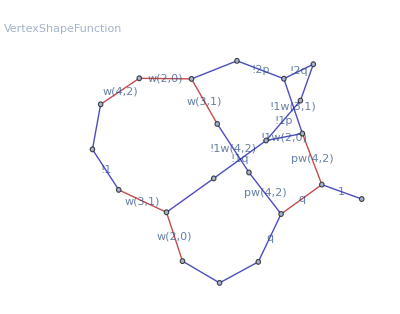

```mathematica
X
```

```mathematica
FullForm[X]
```

Graph[List[ReplaceAll["id",Partition[$Failed,2]],105553137896960,105553137897072,105553137897296,105553137897520,105553137897632,105553137897744,105553137897856,105553137897968,105553137898080,105553137898192,105553137898528,105553137898640,105553137898752,105553137898864,105553137898976,105553137899200,105553137899312,105553137958912,105553137959920,105553137961152,105553137961264],List[UndirectedEdge[105553137898976,105553137897296],UndirectedEdge[105553137899200,105553137897520],UndirectedEdge[105553137897072,105553137899312],UndirectedEdge[105553137898080,105553137899200],UndirectedEdge[105553137899312,105553137898976],UndirectedEdge[105553137897632,105553137898752],UndirectedEdge[105553137897744,105553137898640],UndirectedEdge[105553137898864,105553137898528],UndirectedEdge[105553137896960,105553137898192],UndirectedEdge[105553137898864,105553137897968],UndirectedEdge[105553137898752,105553137897968],UndirectedEdge[105553137898640,105553137897856],UndirectedEdge[105553137898528,105553137897856],UndirectedEdge[105553137896960,105553137897744],UndirectedEdge[105553137897072,105553137897744],UndirectedEdge[105553137897296,105553137897632],UndirectedEdge[105553137897520,105553137897632],UndirectedEdge[105553137898192,105553137961264],UndirectedEdge[105553137898080,105553137961264],UndirectedEdge[105553137897968,105553137961152],UndirectedEdge[105553137897856,105553137961152],UndirectedEdge[105553137961152,105553137959920],UndirectedEdge[105553137961264,105553137959920],UndirectedEdge[105553137959920,105553137958912]],List[Rule[AnnotationRules,List[Rule[UndirectedEdge[105553137897744,105553137898640],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137897296,105553137897632],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137897520,105553137897632],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137961152,105553137959920],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137899200,105553137897520],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137898528,105553137897856],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137897968,105553137961152],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137896960,105553137898192],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137897072,105553137899312],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137897632,105553137898752],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137898192,105553137961264],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137961264,105553137959920],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137898752,105553137897968],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137899312,105553137898976],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137897856,105553137961152],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137898864,105553137898528],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137898080,105553137899200],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule["GraphProperties",List[Rule["id",10000001]]],Rule[UndirectedEdge[105553137898864,105553137897968],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137898976,105553137897296],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137959920,105553137958912],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137896960,105553137897744],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137897072,105553137897744],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137898640,105553137897856],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]],Rule[UndirectedEdge[105553137898080,105553137961264],List[Rule["graphics",List[Rule["targetArrow","standard"]]]]]]],Rule[EdgeLabels,List[Rule[UndirectedEdge[105553137898528,105553137897856],"!2q"],Rule[UndirectedEdge[105553137896960,105553137897744],"w(3,1)"],Rule[UndirectedEdge[105553137961152,105553137959920],"pw(4,2)"],Rule[UndirectedEdge[105553137898640,105553137897856],"!2p"],Rule[UndirectedEdge[105553137898976,105553137897296],"!1"],Rule[UndirectedEdge[105553137898080,105553137899200],""],Rule[UndirectedEdge[105553137898752,105553137897968],"!1q"],Rule[UndirectedEdge[105553137897072,105553137899312],"w(4,2)"],Rule[UndirectedEdge[105553137898864,105553137897968],"!1p"],Rule[UndirectedEdge[105553137897072,105553137897744],"w(2,0)"],Rule[UndirectedEdge[105553137897968,105553137961152],"!1w(2,0)"],Rule[UndirectedEdge[105553137899200,105553137897520],""],Rule[UndirectedEdge[105553137961264,105553137959920],"q"],Rule[UndirectedEdge[105553137897632,105553137898752],""],Rule[UndirectedEdge[105553137897296,105553137897632],"w(3,1)"],Rule[UndirectedEdge[105553137959920,105553137958912],"1"],Rule[UndirectedEdge[105553137897520,105553137897632],"w(2,0)"],Rule[UndirectedEdge[105553137898864,105553137898528],""],Rule[UndirectedEdge[105553137899312,105553137898976],""],Rule[UndirectedEdge[105553137896960,105553137898192],"!1w(4,2)"],Rule[UndirectedEdge[105553137898192,105553137961264],"pw(4,2)"],Rule[UndirectedEdge[105553137897744,105553137898640],""],Rule[UndirectedEdge[105553137898080,105553137961264],"q"],Rule[UndirectedEdge[105553137897856,105553137961152],"!1w(3,1)"]]],Rule[EdgeStyle,List[Rule[UndirectedEdge[105553137898864,105553137897968],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137897520,105553137897632],RGBColor[Rational[2,3],0,0]],Rule[UndirectedEdge[105553137897968,105553137961152],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137898192,105553137961264],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137897072,105553137897744],RGBColor[Rational[2,3],0,0]],Rule[UndirectedEdge[105553137897072,105553137899312],RGBColor[Rational[2,3],0,0]],Rule[UndirectedEdge[105553137897744,105553137898640],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137898976,105553137897296],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137899200,105553137897520],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137961152,105553137959920],RGBColor[Rational[2,3],0,0]],Rule[UndirectedEdge[105553137898528,105553137897856],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137896960,105553137898192],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137959920,105553137958912],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137898080,105553137961264],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137898640,105553137897856],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137898080,105553137899200],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137897296,105553137897632],RGBColor[Rational[2,3],0,0]],Rule[UndirectedEdge[105553137899312,105553137898976],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137961264,105553137959920],RGBColor[Rational[2,3],0,0]],Rule[UndirectedEdge[105553137898752,105553137897968],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137897632,105553137898752],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137898864,105553137898528],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137897856,105553137961152],RGBColor[0,0,Rational[2,3]]],Rule[UndirectedEdge[105553137896960,105553137897744],RGBColor[Rational[2,3],0,0]]]],Rule[VertexShapeFunction,List[Rule[ReplaceAll["id",Partition[$Failed,2]],System`Convert`GraphletDump`DeStringify[ReplaceAll["VertexShapeFunction",Partition[$Failed,2]]]]]],Rule[VertexShape,List[Rule[ReplaceAll["id",Partition[$Failed,2]],System`Convert`GraphletDump`DeStringify[ReplaceAll["VertexShape",Partition[$Failed,2]]]]]],Rule[VertexSize,List[Rule[ReplaceAll["id",Partition[$Failed,2]],System`Convert`GraphletDump`DeStringify[ReplaceAll["VertexSize",Partition[$Failed,2]]]]]],Rule[VertexStyle,List[Rule[ReplaceAll["id",Partition[$Failed,2]],System`Convert`GraphletDump`DeStringify[ReplaceAll["VertexStyle",Partition[$Failed,2]]]]]]]]